# Overlap-subtracted SCET for event shapes v2.0

## Introductory Stuff

```mathematica
p3m/:MakeBoxes[p3m,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","3","-"],p3m];
p3p/:MakeBoxes[p3p,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","3","+"],p3p];
p1m/:MakeBoxes[p1m,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","1","-"],p1m];
p1p/:MakeBoxes[p1p,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","1","+"],p1p];
p2m/:MakeBoxes[p2m,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","2","-"],p2m];
p2p/:MakeBoxes[p2p,TraditionalForm]=InterpretationBox[SubsuperscriptBox["p","2","+"],p2p];
Qp/:MakeBoxes[Qp,TraditionalForm]=InterpretationBox[SuperscriptBox["Q","+"],Qp];
Qm/:MakeBoxes[Qm,TraditionalForm]=InterpretationBox[SuperscriptBox["Q","-"],Qm];
```

```mathematica
p1perp/:MakeBoxes[p1perp,TraditionalForm]=InterpretationBox[SubscriptBox["p","1⊥"],p1perp];
p2perp/:MakeBoxes[p2perp,TraditionalForm]=InterpretationBox[SubscriptBox["p","2⊥"],p2perp];
p3perp/:MakeBoxes[p3perp,TraditionalForm]=InterpretationBox[SubscriptBox["p","3⊥"],p3perp];
```

```mathematica
x13/:MakeBoxes[x13,TraditionalForm]=InterpretationBox[SubscriptBox["x","13"],x13];x23/:MakeBoxes[x23,TraditionalForm]=InterpretationBox[SubscriptBox["x","23"],x23];
x12/:MakeBoxes[x12,TraditionalForm]=InterpretationBox[SubscriptBox["x","12"],x12];
```

```mathematica
nb/:MakeBoxes[nb,TraditionalForm]=InterpretationBox[OverscriptBox["n","_"],nb];
```

```mathematica
<<HypExp`
(* $LoadPhi=True *)
$LoadFeynArts=$LoadPhi=False;
Needs["HighEnergyPhysics`FeynCalc`"]
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, mm2___List, x_] is Protected.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1___List, mm2 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/luke/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

## SCET variable transformations

Full energy-momentum conservation

```mathematica
dotsubs={SP[n,p1]->p1p,SP[n,p2]->p2p,SP[n,q]->p3p,SP[nb,p1]->p1m,SP[nb,p2]->p2m,SP[nb,q]->p3m,SP[p1,q]->1/2((p1p+p3p)(p1m+p3m)-(p1perp+ p3perp)^2),SP[p2,q]->1/2((p2p+p3p)(p2m+p3m)-(p2perp+ p3perp)^2),SP[p1,p2]->1/2((p1p+p2p)(p1m+p2m)-(p1perp+ p2perp)^2)}
```

{n·p1→p_1^+,n·p2→p_2^+,n·q→p_3^+,n̄·p1→p_1^-,n̄·p2→p_2^-,n̄·q→p_3^-,p1·q→1/2 ((p_1^-+p_3^-) (p_1^++p_3^+)-(p_(1⊥)+p_(3⊥))^2),p2·q→1/2 ((p_2^-+p_3^-) (p_2^++p_3^+)-(p_(2⊥)+p_(3⊥))^2),p1·p2→1/2 ((p_1^-+p_2^-) (p_1^++p_2^+)-(p_(1⊥)+p_(2⊥))^2)}

```mathematica
nsubs={SP[n,n]->0,SP[nb,nb]->0,SP[n,nb]->2,SP[p1,p1]->0,SP[p2,p2]->0,SP[q,q]->0}
nsubsD=ChangeDimension[nsubs,D]//FCE
```

{n^2→0,(n̄)^2→0,n·n̄→2,p1^2→0,p2^2→0,q^2→0}

{n^2→0,(n̄)^2→0,n·n̄→2,p1^2→0,p2^2→0,q^2→0}

```mathematica
conssubs={p1perp->-p3perp,p3perp->Sqrt[p3p p3m] p3perphat,p2m->0,p1p->p3p p3m/p1m, p1m->1-p3m,p2p->1-p3p-p1p,p3perphat^2->1,p2perp->0}
```

{p_(1⊥)→-p_(3⊥),p_(3⊥)→√(p_3^- p_3^+) p3perphat,p_2^-→0,p_1^+→(p_3^- p_3^+)/p_1^-,p_1^-→1-p_3^-,p_2^+→-p_1^+-p_3^++1,p3perphat^2→1,p_(2⊥)→0}

```mathematica
psubs={x13->(2 SP[p1,q]//.dotsubs//ExpandAll)//.conssubs//FullSimplify,x23->(2 SP[p2,q]//.dotsubs//ExpandAll)//.conssubs//FullSimplify}

xsubs=(Solve[{x13==(x13/.psubs),x23==(x23/.psubs)},{p3p,p3m}]//FullSimplify)[[1]]
```

{x_13→p_3^+/(1-p_3^-),x_23→(p_3^+ p_3^-)/(p_3^--1)+p_3^-}

{p_3^+→(x_23 x_13)/(x_13-1)+x_13,p_3^-→-x_23/(x_13-1)}

virtual graphs are scaleless in DR, so zero contribution.  Just counterterm and C2.

```mathematica
C2=2(-1/2 Log[μ^2]^2-3/2 Log[μ^2]-4+7 π^2/12)//Expand
```

-log^2(μ^2)-3 log(μ^2)+(7 π^2)/6-8

```mathematica
Z2=2 Series[1/ϵ^2+3/2/ϵ+1/ϵ Log[μ^2],{ϵ,0,0}]
```

2/ϵ^2+(2 (log(μ^2)+3/2))/ϵ+O(ϵ^1)

```mathematica
pnb=GS[nb].GS[n]/4
```

1/4 (γ·n̄).(γ·n)

```mathematica
msprefactor=(2 Exp[ϵ EulerGamma] μ^(2 ϵ))/(Gamma[1-ϵ] (1-x1)^ϵ (1-x2)^ϵ (x1+x2-1)^ϵ)/.x2->1-x13/.x1->1-x23
```

(2 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^-ϵ μ^(2 ϵ))/(1-ϵ)

## SCET amplitudes

### QCD amplitude ... make sure we can do this right

Note the factor of 1/(1-ϵ) in the amplitude squared is pulled out by def’n (see M&S)

the right answer ...

```mathematica
dσfullx=FullSimplify[(2 μ^(2 ϵ) Exp[ϵ EulerGamma] (x1^2+x2^2-ϵ (2-x1-x2)^2))/((((1-x1)^(1+ϵ) (1-x2)^(1+ϵ)) Gamma[1-ϵ]) (x1+x2-1)^ϵ)/.x2->1-x13/.x1->1-x23]
```

(2 ⅇ^(ℽ ϵ) (x_13)^(-ϵ-1) (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) (-(x_13+x_23)^2 ϵ+(x_13-1)^2+(x_23-1)^2) μ^(2 ϵ))/(1-ϵ)

```mathematica
qcdamp1=(ChangeDimension[-Spinor[p1,0].(2 FV[p1,α]+GA[α]. GS[q]).GA[μ].Spinor[p2,0]/(2 SP[p1,q]),D]//DiracSimplify//FCE)//.nsubsD
qcdamp2=(ChangeDimension[Spinor[p1,0].GA[μ].(2 FV[p2,α]+ GS[q].GA[α]).Spinor[p2,0] /(2 SP[p2,q]),D]//DiracSimplify//FCE)//.nsubsD
```

-(p1^α φ(p1).γ^μ.φ(p2))/(p1·q)-(φ(p1).γ^α.(γ·q).γ^μ.φ(p2))/(2 p1·q)

(p2^α φ(p1).γ^μ.φ(p2))/(p2·q)+(φ(p1).γ^μ.(γ·q).γ^α.φ(p2))/(2 p2·q)

```mathematica
r11QCD=(ChangeDimension[(((FermionSpinSum[qcdamp1 (ComplexConjugate[qcdamp1]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
r22QCD=(ChangeDimension[(((FermionSpinSum[qcdamp2  (ComplexConjugate[qcdamp2]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD

r12QCD=(ChangeDimension[(((FermionSpinSum[qcdamp1  (ComplexConjugate[qcdamp2]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
r21QCD=(ChangeDimension[(((FermionSpinSum[qcdamp2  (ComplexConjugate[qcdamp1]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
```

(2 D^2 p1·q p2·q-8 D p1·q p2·q+8 p1·q p2·q)/(p1·q)^2

(2 D^2 p1·q p2·q-8 D p1·q p2·q+8 p1·q p2·q)/(p2·q)^2

-(-2 D^2 p1·q p2·q+12 D p1·q p2·q-16 p1·q p2·q)/(p1·q p2·q)-(4 p1·p2 (2 p1·p2-D p1·p2))/(p1·q p2·q)-(2 (4 p1·p2 p2·q-2 D p1·p2 p2·q))/(p1·q p2·q)-(2 (4 p1·p2 p1·q-2 D p1·p2 p1·q))/(p1·q p2·q)

-(-2 D^2 p1·q p2·q+12 D p1·q p2·q-16 p1·q p2·q)/(p1·q p2·q)-(4 p1·p2 (2 p1·p2-D p1·p2))/(p1·q p2·q)-(2 (4 p1·p2 p2·q-2 D p1·p2 p2·q))/(p1·q p2·q)-(2 (4 p1·p2 p1·q-2 D p1·p2 p1·q))/(p1·q p2·q)

```mathematica
qcdratencalc1 = ChangeDimension[(r11QCD+r22QCD+r12QCD+r21QCD)/8/(-1+D/2),4]//FCE// FullSimplify
```

(2 (D-4) p1·q p2·q+(D-2) (p1·q)^2+(D-2) (p2·q)^2+4 p1·p2 (p1·q+p2·q)+4 (p1·p2)^2)/(2 p1·q p2·q)

```mathematica
qcdratencalc=qcdratencalc1/.D->4-2ϵ//.SP[p1,q]->x13/2//.SP[p2,q]-> x23/2//.SP[p1,p2]-> x12/2/.x12->1-x13-x23//FullSimplify
```

((x_13+x_23)^2 (-ϵ)+(x_13-2) x_13+(x_23-2) x_23+2)/(x_13 x_23)

```mathematica
qcdratencalc/.ϵ->0//ExpandAll//Together
dσfullx/msprefactor/.ϵ->0//ExpandAll//Together
```

((x_13)^2-2 x_13+(x_23)^2-2 x_23+2)/(x_13 x_23)

((x_13)^2-2 x_13+(x_23)^2-2 x_23+2)/(x_13 x_23)

got it right!

```mathematica
Series[qcdratencalc,{ϵ,0,1}]//FullSimplify//ExpandAll
```

(x_13/x_23-2/x_23+x_23/x_13+2/(x_23 x_13)-2/x_13)+(-x_13/x_23-x_23/x_13-2) ϵ+O(ϵ^2)

```mathematica
Series[dσfullx/msprefactor,{ϵ,0,1}]//FullSimplify//ExpandAll//Together
```

(x_13/x_23-2/x_23+x_23/x_13+2/(x_23 x_13)-2/x_13)+(-x_13/x_23-x_23/x_13-2) ϵ+O(ϵ^2)

### SCET amplitude

```mathematica
scetnamp1=(ChangeDimension[-Spinor[p1,0].(2 FV[p1,α]+GA[α]. GS[q]).pnb.GA[μ].pnb.Spinor[p2,0]/(2 SP[p1,q]),D]//DiracSimplify//FCE)//.nsubsD
scetnamp2=(ChangeDimension[Spinor[p1,0].pnb.GA[μ].pnb.Spinor[p2,0] FV[nb,α]/SP[nb,q],D]//DiracSimplify//FCE)//.nsubsD
```

-(p1^α φ(p1).γ^μ.(γ·n̄).(γ·n).φ(p2))/(4 p1·q)+(p1^α (n̄)^μ φ(p1).(γ·n).φ(p2))/(2 p1·q)+((n̄)^μ φ(p1).γ^α.(γ·q).(γ·n).φ(p2))/(4 p1·q)-(φ(p1).γ^α.(γ·q).γ^μ.(γ·n̄).(γ·n).φ(p2))/(8 p1·q)

((n̄)^α φ(p1).γ^μ.(γ·n̄).(γ·n).φ(p2))/(4 n̄·q)-((n̄)^α (n̄)^μ φ(p1).(γ·n).φ(p2))/(2 n̄·q)

```mathematica
r11n=(ChangeDimension[(((FermionSpinSum[scetnamp1 (ComplexConjugate[scetnamp1]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
r22n=(ChangeDimension[(((FermionSpinSum[scetnamp2  (ComplexConjugate[scetnamp2]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD

r12n=(ChangeDimension[(((FermionSpinSum[scetnamp1  (ComplexConjugate[scetnamp2]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
r21n=(ChangeDimension[(((FermionSpinSum[scetnamp2  (ComplexConjugate[scetnamp1]/.μ->ν/.α->β)//ExpandAll]*MetricTensor[μ,ν,Dimension->D]MetricTensor[α,β,Dimension->D])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
```

(16 D^2 n·p2 p1·q n̄·q-64 D n·p2 p1·q n̄·q+64 n·p2 p1·q n̄·q)/(16 (p1·q)^2)

0

-(n̄·p1 (16 n·p2 n̄·p1-8 D n·p2 n̄·p1))/(4 p1·q n̄·q)-(32 n·p2 n̄·p1 n̄·q-16 D n·p2 n̄·p1 n̄·q)/(8 p1·q n̄·q)

-(n̄·p1 (16 n·p2 n̄·p1-8 D n·p2 n̄·p1))/(4 p1·q n̄·q)-(32 n·p2 n̄·p1 n̄·q-16 D n·p2 n̄·p1 n̄·q)/(8 p1·q n̄·q)

```mathematica
scetratencalc1 = ChangeDimension[(r11n+r22n+r12n+r21n)/4/(-1+D/2),4]//FCE// FullSimplify
```

(n·p2 ((D-2) (n̄·q)^2+4 n̄·p1 n̄·q+4 (n̄·p1)^2))/(2 p1·q n̄·q)

```mathematica
scetratencalc=scetratencalc1/.D->4-2ϵ//FullSimplify
```

(n·p2 (2 n̄·p1 n̄·q+2 (n̄·p1)^2-(ϵ-1) (n̄·q)^2))/(p1·q n̄·q)

```mathematica
Series[scetratencalc,{ϵ,0,22}]//Simplify//Normal
```

(n·p2 (2 n̄·p1 n̄·q+2 (n̄·p1)^2+(n̄·q)^2))/(p1·q n̄·q)-(ϵ n·p2 n̄·q)/(p1·q)

agrees with M&S using multipole expansion for momenta

```mathematica
aFsq=FullSimplify[(1+x1^2)/((1-x1) (1-x2))-(ϵ (1-x1))/(1-x2)/.x2->1-x13/.x1->1-x23]
```

(x_23 (x_23 (-ϵ)+x_23-2)+2)/(x_13 x_23)

```mathematica
Series[scetratencalc/.SP[n,p2]->1/.SP[nb,q]->x23/.SP[p1,q]->x13/.SP[p1,nb]->1-x23,{ϵ,0,1}]//Expand
```

((x_23)^2-2 x_23+2)/(x_13 x_23)-(x_23 ϵ)/x_13+O(ϵ^2)

```mathematica
Series[aFsq,{ϵ,0,1}]
```

((x_23)^2-2 x_23+2)/(x_13 x_23)-(x_23 ϵ)/x_13+O(ϵ^2)

## SCET rate

```mathematica
dσnx=msprefactor Normal[(Series[scetratencalc,{ϵ,0,2}]//.dotsubs//ExpandAll)//.conssubs//.xsubs//FullSimplify]
```

(2 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^-ϵ ((4 (x_13-1)^2+4 x_23 (x_13-1)+2 (x_23)^2)/(x_13 x_23)-(2 x_23 ϵ)/x_13) μ^(2 ϵ))/(1-ϵ)

Jacobean to switch to p3p, p3m variables

```mathematica
pjacob=FullSimplify[Det[{{D[x13/.psubs,p3p],D[x13/.psubs,p3m]},{D[x23/.psubs,p3p],D[x23/.psubs,p3m]}}],{p3m>0, p3p>0,p3m<1,p3m<1}]
```

-(p_3^-+p_3^+-1)/((p_3^--1)^2)

```mathematica
msprefactorp=FullSimplify[msprefactor/.psubs,{p3m>0,p3m<1,p3p>0,p3p<1}]//.a_^(-2 ϵ):>Together[a]^(-2 ϵ)//.(a_/(p3m-1))^b_->(-a)^b/(1-p3m)^b/.(p3m p3p)^b_->p3p^b p3m^b
```

(2 ⅇ^(ℽ ϵ) (1-p_3^-)^(2 ϵ) (p_3^-)^-ϵ (-p_3^--p_3^++1)^(-2 ϵ) (p_3^+)^-ϵ μ^(2 ϵ))/(1-ϵ)

```mathematica
dσnp=msprefactorp*pjacob*Normal[(Series[scetratencalc,{ϵ,0,2}]//.dotsubs//ExpandAll)//.conssubs//FullSimplify]//FullSimplify
```

-(4 ⅇ^(ℽ ϵ) (1-p_3^-)^(2 (ϵ-1)) (p_3^-)^(-ϵ-1) (-p_3^--p_3^++1)^(2-2 ϵ) (p_3^+)^(-ϵ-1) (p_3^- (p_3^- (ϵ-1)+2)-2) μ^(2 ϵ))/(1-ϵ)

```mathematica
dσnold= (2 μ^(2 ϵ) Exp[ϵ EulerGamma] (p3m k3p)^-ϵ ((p3m (1- ϵ))/Q+(2 (Q-p3m))/p3m))/(Gamma[1-ϵ] (Q k3p))/.k3p->p3p/.Q->1//PowerExpand
```

(2 ⅇ^(ℽ ϵ) (p_3^-)^-ϵ (p_3^+)^(-ϵ-1) (p_3^- (1-ϵ)+(2 (1-p_3^-))/p_3^-) μ^(2 ϵ))/(1-ϵ)

```mathematica
dσnp/dσnold//FullSimplify
```

2 (1-p_3^-)^(2 (ϵ-1)) (-p_3^--p_3^++1)^(2-2 ϵ)

```mathematica
dσnp/dσnold//FullSimplify
Series[dσnp/dσnold,{p3p,0,1}]//FullSimplify
```

2 (1-p_3^-)^(2 (ϵ-1)) (-p_3^--p_3^++1)^(2-2 ϵ)

2-(4 p_3^+ (ϵ-1))/(p_3^--1)+O((p_3^+)^2)

## Phase space

### get boundaries where different particles define the thrust axis

```mathematica
E1=1/2(p1p+p1m)//.conssubs//.xsubs//FullSimplify
E2=1/2(p2p+p2m)//.conssubs//.xsubs//FullSimplify
E3=1/2(p3p+p3m)//.conssubs//.xsubs//FullSimplify
```

1/2 (1-x_23)

1/2 (1-x_13)

1/2 (x_13+x_23)

```mathematica
E12bdyx=(x23/.Solve[E1==E2,x23]//FullSimplify)[[1]]
E23bdyx=(x23/.Solve[E2==E3,x23]//FullSimplify)[[1]]
E13bdyx=(x23/.Solve[E1==E3,x23]//FullSimplify)[[1]]
```

x_13

1-2 x_13

1/2 (1-x_13)

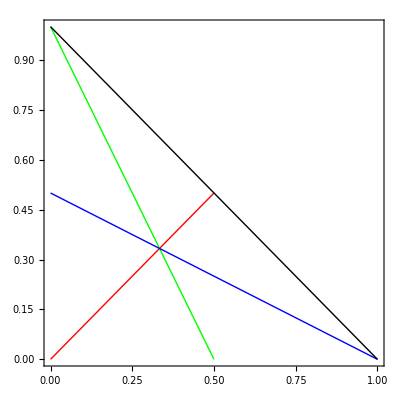

```mathematica
bdryplotx=Plot[{E12bdyx,E23bdyx,E13bdyx,1-x13},{x13,0,1},Frame->True,PlotRange->{0,1},RegionFunction->Function[{x13,x23},x13<1-x23+.0001],AspectRatio->1,PlotStyle->{Red,Green,Blue,Black}]
```

### work out thrust dot products in when p1, p2 or p3 defines the thrust axis.

#### p1 thrust axis

```mathematica
p1mag=FullSimplify[Sqrt[p1perp^2+1/4(p1p-p1m)^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]
```

(p_3^- (p_3^-+p_3^+-2)+1)/(2-2 p_3^-)

```mathematica
p3dott1=FullSimplify[(p3perp p1perp+1/4(p3p-p3m)(p1p-p1m))/p1mag//.conssubs]
```

(p_3^- (p_3^-+p_3^+-1)^2-p_3^+)/(2 (p_3^- (p_3^-+p_3^+-2)+1))

```mathematica
p2dott1=FullSimplify[(p2perp p1perp+1/4(p2p-p2m)(p1p-p1m))/p1mag//.conssubs]
```

-((p_3^-+p_3^+-1) ((p_3^-)^2-(p_3^++2) p_3^-+1))/(2 ((p_3^--1)^3+p_3^- p_3^+ (p_3^--1)))

#### p2 thrust axis

```mathematica
p2mag=FullSimplify[Sqrt[p2perp^2+1/4(p2p-p2m)^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1-p3m}]
```

(p_3^-+p_3^+-1)/(2 (p_3^--1))

```mathematica
p3dott2=FullSimplify[(p3perp p2perp+1/4(p3p-p3m)(p2p-p2m))/p2mag//.conssubs]
```

1/2 (p_3^+-p_3^-)

```mathematica
p1dott2=FullSimplify[(p1perp p2perp+1/4(p1p-p1m)(p2p-p2m))/p2mag//.conssubs]
```

((p_3^-)^2-(p_3^++2) p_3^-+1)/(2 (p_3^--1))

#### p3 thrust axis

```mathematica
p3mag=FullSimplify[Sqrt[p3perp^2+1/4(p3p-p3m)^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]
```

1/2 (p_3^-+p_3^+)

```mathematica
p1dott3=FullSimplify[(p1perp p3perp+1/4(p1p-p1m)(p3p-p3m))/p3mag//.conssubs]
```

(p_3^+-p_3^- (p_3^-+p_3^+-1)^2)/(2 (p_3^--1) (p_3^-+p_3^+))

```mathematica
p2dott3=FullSimplify[(p2perp p3perp+1/4(p2p-p2m)(p3p-p3m))/p3mag//.conssubs]
```

-((p_3^--p_3^+) (p_3^-+p_3^+-1))/(2 (p_3^--1) (p_3^-+p_3^+))

### Thrust

#### p1 thrust axis

```mathematica
t2r1=1/2(p2p+p2m)+p2dott1//.conssubs//FullSimplify
t3r1=1/2(p3p+p3m)+p3dott1//.conssubs//FullSimplify
```

(p_3^- p_3^+ (p_3^-+p_3^+-1))/((p_3^--1)^3+p_3^- p_3^+ (p_3^--1))

(p_3^- (p_3^-+p_3^+-1)^2)/(p_3^- (p_3^-+p_3^+-2)+1)

well this is simple ...

```mathematica
t23=t2r1+t3r1//FullSimplify//Together//FullSimplify
```

(p_3^+ p_3^-)/(p_3^--1)+p_3^-

#### p2 thrust axis

```mathematica
t1r2=1/2(p1p+p1m)+p1dott2//.conssubs//FullSimplify
t3r2=1/2(p3p+p3m)+p3dott2//.conssubs//FullSimplify
```

(p_3^- p_3^+)/(1-p_3^-)

p_3^+

of course the t axis is just the z axis by definition here so it’s simple

```mathematica
t13=t1r2+t3r2//Expand//FullSimplify
```

p_3^+/(1-p_3^-)

#### p3 thrust axis

```mathematica
t1r3=1/2(p1p+p1m)+p1dott3//.conssubs//FullSimplify
t2r3=1/2(p2p+p2m)+p2dott3//.conssubs//FullSimplify
```

-(p_3^- (p_3^-+p_3^+-1)^2)/((p_3^--1) (p_3^-+p_3^+))

(p_3^+ (p_3^-+p_3^+-1))/((p_3^--1) (p_3^-+p_3^+))

again, this is simple ...

```mathematica
t12=t1r3+t2r3//FullSimplify//Together//FullSimplify
```

-p_3^--p_3^++1

#### x variables

```mathematica
t12x=t12//.xsubs//FullSimplify
t13x=t13//.xsubs//FullSimplify
t23x=t23//.xsubs//FullSimplify
```

-x_13-x_23+1

x_13

x_23

#### Plots

```mathematica
τfn[x1_,x2_]:=If[x1<1/3,
				If[x2>(E12bdyx/.x1->x13/.x2->x23),
				If[x2<E23bdyx,(t13x/.x1->x13/.x2->x23),(t12x/.x1->x13/.x2->x23)],
(t23x/.x1->x13/.x2->x23)],
				If[x2>(E13bdyx/.x1->x13/.x2->x23),(t12x/.x1->x13/.x2->x23),(t23x/.x1->x13/.x2->x23)]]
```

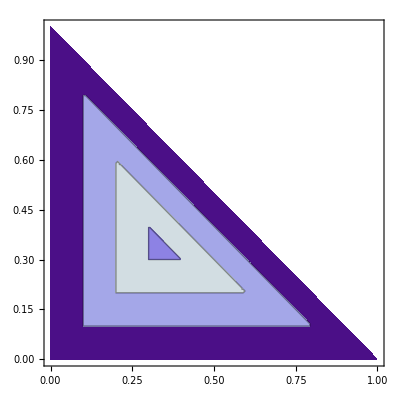

```mathematica
τcontoursx=ContourPlot[τfn[x13,x23],{x13,0,1},{x23,0,1},RegionFunction->Function[{p3p,p3m},p3m<1-p3p],Contours->{.1,.2,.3,.4,.5,.6,.7,.8,.9}]
```

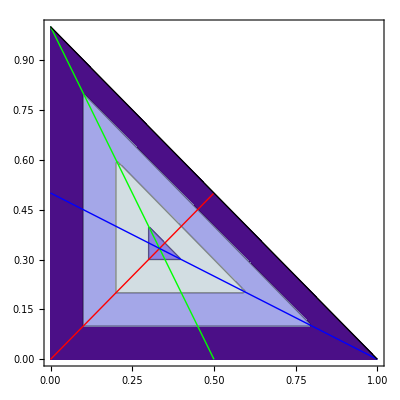

```mathematica
Show[τcontoursx,bdryplotx]
```

### Jet broadening

#### p1 thrust axis

```mathematica
b2r1=FullSimplify[Sqrt[p2perp^2+1/4(p2p-p2m)^2-p2dott1^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Abs[p3m+p3p-1]->1-p3p-p3m
b3r1=FullSimplify[Sqrt[p3perp^2+1/4(p3p-p3m)^2-p3dott1^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Abs[p3m+p3p-1]->1-p3p-p3m
```

((-p_3^--p_3^++1) √(p_3^- p_3^+))/(p_3^- (p_3^-+p_3^+-2)+1)

((-p_3^--p_3^++1) √(p_3^- p_3^+))/(p_3^- (p_3^-+p_3^+-2)+1)

```mathematica
b23=1/2(b2r1+b3r1)//FullSimplify
```

-(√(p_3^- p_3^+) (p_3^-+p_3^+-1))/(p_3^- (p_3^-+p_3^+-2)+1)

#### p2 thrust axis

```mathematica
b1r2=FullSimplify[Sqrt[p1perp^2+1/4(p1p-p1m)^2-p1dott2^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Abs[p3m+p3p-1]->1-p3p-p3m
b3r2=FullSimplify[Sqrt[p3perp^2+1/4(p3p-p3m)^2-p3dott2^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Abs[p3m+p3p-1]->1-p3p-p3m
```

√(p_3^- p_3^+)

√(p_3^- p_3^+)

again, the t axis is just the z axis by definition here so it’s simple

```mathematica
b13=1/2(b1r2+b3r2)//Expand//FullSimplify
```

√(p_3^- p_3^+)

#### p3 thrust axis

```mathematica
b1r3=FullSimplify[Sqrt[p1perp^2+1/4(p1p-p1m)^2-p1dott3^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Sqrt[a_ (p3m+p3p-1)^2]->(1-p3m-p3p) Sqrt[a]/.Sqrt[a_/(p3m-1)^2/(p3m+p3p)^2]->Sqrt[a]/(1-p3m)/(p3m+p3p)//FullSimplify
b2r3=FullSimplify[Sqrt[p2perp^2+1/4(p2p-p2m)^2-p2dott3^2]//.conssubs,{p3m>0,p3m<1,p3p>0,p3p<1}]/.Sqrt[a_ (p3m+p3p-1)^2]->(1-p3m-p3p) Sqrt[a]/.Sqrt[a_/(p3m-1)^2/(p3m+p3p)^2]->Sqrt[a]/(1-p3m)/(p3m+p3p)//FullSimplify
```

(√(p_3^- p_3^+) (p_3^-+p_3^+-1))/((p_3^--1) (p_3^-+p_3^+))

(√(p_3^- p_3^+) (p_3^-+p_3^+-1))/((p_3^--1) (p_3^-+p_3^+))

```mathematica
b12=1/2(b1r3+b2r3)//FullSimplify//Together//FullSimplify
```

(√(p_3^- p_3^+) (p_3^-+p_3^+-1))/((p_3^--1) (p_3^-+p_3^+))

#### x variables

```mathematica
b12x=FullSimplify[b12//.xsubs,{x13>0,x13<1}]
b13x=FullSimplify[b13//.xsubs,{x13>0,x13<1}]/.Sqrt[a_/(x13-1)^2]->Sqrt[a]/(1-x13)
b23x=FullSimplify[b23//.xsubs,{x13>0,x13<1}]
```

(√(-x_13 x_23 (x_13+x_23-1)))/(x_13+x_23)

(√(-x_13 x_23 (x_13+x_23-1)))/(1-x_13)

-(√(-x_13 x_23 (x_13+x_23-1)))/(x_23-1)

#### Plots

```mathematica
Bfn[x1_,x2_]:=If[x1<1/3,
				If[x2>(E12bdyx/.x1->x13/.x2->x23),
				If[x2<E23bdyx,(b13x/.x1->x13/.x2->x23),(b12x/.x1->x13/.x2->x23)],
(b23x/.x1->x13/.x2->x23)],
				If[x2>(E13bdyx/.x1->x13/.x2->x23),(b12x/.x1->x13/.x2->x23),(b23x/.x1->x13/.x2->x23)]]
```

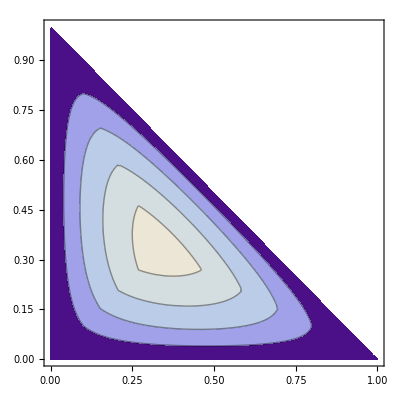

```mathematica
Bcontoursx=ContourPlot[Bfn[x13,x23],{x13,0,1},{x23,0,1},RegionFunction->Function[{p3p,p3m},p3m<1-p3p],Contours->{.5,.1,.15,.2,.25,.3,.35,.4,.45}]
```

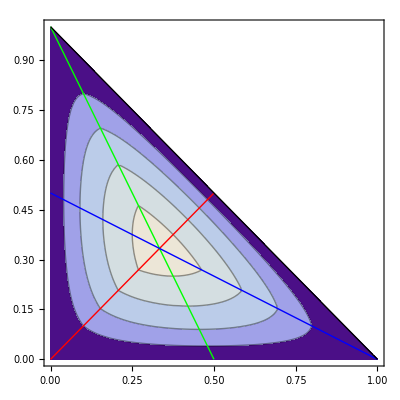

```mathematica
Show[Bcontoursx,bdryplotx]
```

## integrate

### thrust

#### first, the n-collinear

```mathematica
dσnx
```

(2 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^-ϵ ((4 (x_13-1)^2+4 x_23 (x_13-1)+2 (x_23)^2)/(x_13 x_23)-(2 x_23 ϵ)/x_13) μ^(2 ϵ))/(1-ϵ)

```mathematica
ia1=Integrate[dσnx,{x13,0,x23},GenerateConditions->False]/.(x23 b_)^c_->x23^c b^c//FullSimplify
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2) -ϵϵ1-ϵ-x_23/(x_23-1))/ϵ-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ia2=ia1/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2))/(ϵ 1-ϵ)-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ia3=Integrate[ia2,{x23,0,τ},GenerateConditions->False]
```

-1/((1-2 ϵ)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) (2 τ ϵ^2 (9 ϵ^2-17 ϵ+8) 1-2 ϵϵ2-2 ϵ2 τ+(2 ϵ-1) (2 τ^2 (2-3 ϵ) ϵ^2 2-2 ϵϵ3-2 ϵ2 τ+τ^2 ϵ (2 ϵ^3-4 ϵ^2+3 ϵ-1) 2-2 ϵϵ3-2 ϵτ+(ϵ-1)^2 (-((ϵ-2) -2 ϵϵ1-2 ϵτ+3 ϵ -2 ϵϵ1-2 ϵ2 τ)))-4 τ ϵ (ϵ-1)^2 1-2 ϵϵ2-2 ϵτ)

```mathematica
ia4=Series[ia3,{ϵ,0,0}]//Normal
```

1/3 (-12 τ^2 log(μ)+48 τ log(μ)-48 log(μ) log(τ)+24 log^2(μ)-24 2τ+15 τ^2+6 τ^2 log(1-τ)+12 τ^2 log(τ)+18 τ+24 log^2(τ)-24 τ log(1-τ)-48 τ log(τ)+18 log(1-τ)-π^2)+4/ϵ^2-(2 (-4 log(μ)+τ^2-4 τ+4 log(τ)))/ϵ

```mathematica
ia5=(Series[ia4,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify
```

8 log^2(μ/τ)+4/ϵ^2+(8 log(μ/τ))/ϵ-π^2/3

```mathematica
ib1=Integrate[dσnx,{x13,0,τ},GenerateConditions->False]
```

(4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ (((x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2) -ϵϵ1-ϵ-τ/(x_23-1))/ϵ-((τ+x_23-1) (τ/(x_23-1)+1)^-ϵ ((x_23-3) (ϵ-1)+τ (2 ϵ-1)))/(ϵ-1)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib2=ib1/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

(4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2)/ϵ-((τ+x_23-1) (τ/(x_23-1)+1)^-ϵ ((x_23-3) (ϵ-1)+τ (2 ϵ-1)))/(ϵ-1)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib3=Integrate[ib2,{x23,τ,1-2τ},GenerateConditions->False]
```

(4 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^-ϵ (((1-2 τ) τ)^-ϵ ((ϵ-1) τ^ϵ ((ϵ-1) ((ϵ-2)^2 -ϵϵ1-ϵ1-2 τ-(1-2 τ)^2 ϵ (2 ϵ^2-2 ϵ+1) 2-ϵϵ3-ϵ1-2 τ)-2 (2 τ-1) (ϵ-2) ϵ 1-ϵϵ2-ϵ1-2 τ)+ϵ (-τ/(τ-1))^ϵ ((ϵ-1) ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵϵ3-ϵ(2 τ-1)/(τ-1)+(τ-1) (ϵ-2) (-τ+(2 τ-3) ϵ+3) -ϵϵ1-ϵ(2 τ-1)/(τ-1))-(2 τ-1) (ϵ-2) ϵ (-2 τ+(3 τ-4) ϵ+4) 1-ϵϵ2-ϵ(2 τ-1)/(τ-1)))-(-(τ-1) τ)^-ϵ ((ϵ-1) (1-τ)^ϵ ((ϵ-1) ((ϵ-2)^2 -ϵϵ1-ϵτ-τ^2 ϵ (2 ϵ^2-2 ϵ+1) 2-ϵϵ3-ϵτ)+2 τ (ϵ-2) ϵ 1-ϵϵ2-ϵτ)+ϵ ((ϵ-1) (τ^2 (ϵ-1) ϵ 2-ϵϵ3-ϵ-τ/(τ-1)+(τ-1) (ϵ-2) (-τ+(2 τ-3) ϵ+3) -ϵϵ1-ϵ-τ/(τ-1))+τ (ϵ-2) ϵ (-2 τ+(3 τ-4) ϵ+4) 1-ϵϵ2-ϵ-τ/(τ-1)))))/((ϵ-2) (ϵ-1)^2 ϵ^2 (2 ϵ-1) 1-ϵ)

```mathematica
ib4=Series[ib3,{ϵ,0,0}]//Normal
```

4 ((-3 τ^2-8 τ-4 log(1-τ)+4 log(τ)-4 log((1-2 τ) τ)+4 log(-(τ-1) τ)+3) (log(μ)-(log(τ))/2+9/4)+1/2 (-4 21-2 τ+4 2τ+(3 τ^2)/2-4 τ^2 log(τ)+4 τ^2 log(2 τ)-(-6 τ^2+4 τ+4 log(τ)-15) log((1-2 τ) τ)+(-3 τ^2+12 τ+4 log(1-τ)-18) log(-(τ-1) τ)+19 τ-2 log^2(1-τ)+2 log^2(τ)+2 log^2((1-2 τ) τ)-2 log^2(-(τ-1) τ)-4 τ log(τ)+4 τ log(2 τ)+9 log(1-τ)-9 log(τ)-2 (τ-3) (τ-1) log(-τ/(τ-1))-13/2))+(2 (-3 τ^2-8 τ-4 log(1-τ)+4 log(τ)-4 log((1-2 τ) τ)+4 log(-(τ-1) τ)+3))/ϵ

```mathematica
ib5=(Series[ib4,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

16 log(τ) log(μ/τ)+12 log(μ/τ)+4 log^2(τ)+6 log(τ)+(8 log(τ))/ϵ+6/ϵ-(4 π^2)/3+14

```mathematica
ic1indef=Integrate[dσnx,x13]
ic1=((ic1indef/.x13->1/2(1-x23))-(ic1indef/.x13->0))/. 0^(a_)->0
```

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) ((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵx_13/(1-x_23)-2 (x_13)^2 ϵ 2-ϵϵ3-ϵx_13/(1-x_23))-2 x_13 (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵx_13/(1-x_23))

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)2^(ϵ+2) ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (1/2 (x_23-1)-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((1/2 (1-x_23)+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1)+2 x_23-2)-1/2 (1-x_23)^2 ϵ 2-ϵϵ3-ϵ1/2)-(1-x_23) (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2)

```mathematica
ic2indef=Integrate[ic1,x23]
ic2=(ic2indef/.x23->1)-(ic2indef/.x23->1-2τ)
```

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) (x_23)^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-3 x_23 (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵx_23)-(ϵ-1) (2 x_23 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵx_23+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵx_23-2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-ϵ 2-ϵϵ3-ϵ1/2 ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+(ϵ-2) -ϵ2 ϵ1-ϵx_23))))

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-(3 (ϵ-2) ϵ 1-2 ϵ 2-ϵ)/(2-3 ϵ))-(ϵ-1) ((2 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-2 ϵ 2-ϵ)/(2-3 ϵ)+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (((ϵ-1) ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)-(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-ϵ 2-ϵϵ3-ϵ1/2 ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+((ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ)))))-1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (1-2 τ)^-ϵ (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-3 (1-2 τ) (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵ1-2 τ)-(ϵ-1) (2 (1-2 τ) (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵ1-2 τ+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵ1-2 τ-2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-ϵ 2-ϵϵ3-ϵ1/2 ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+(ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ))))

```mathematica
ic3=Series[ic2,{ϵ,0,0}]//Normal
```

1/3 (48 τ^2 log(μ)+48 τ log(μ)+48 log(μ) log(1-2 τ)+48 21-2 τ+30 τ^2-24 τ^2 log(1-2 τ)-48 τ^2 log(2 τ)+24 τ^2 log(2)+150 τ-12 log^2(1-2 τ)-24 τ log(1-2 τ)-48 τ log(2 τ)+24 τ log(2)+24 log(2) log(1-2 τ)+39 log(1-2 τ)-8 π^2)+(8 (τ^2+τ+log(1-2 τ)))/ϵ

```mathematica
ic4=(Series[ic3,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

0

```mathematica
τn=Series[ia5+ib5+ic4/.Log[μ/τ]->1/2 Log[μ^2]-Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
2 Log[μsq/τ]- Log[μsq/τ^2]//PowerExpand//Expand
2Log[μsq/τ]^2-Log[μsq/τ^2]^2//PowerExpand//Expand
Log[μsq/τ]//PowerExpand//Expand
```

log(μsq)

log^2(μsq)-2 log^2(τ)

log(μsq)-log(τ)

```mathematica
τnSCfactor=Series[Expand[Normal[τn]]/. Log[μ^2]/ϵ->2 Log[μ^2/τ]/ϵ- Log[μ^2/τ^2]/ϵ/.  Log[μ^2]^2->2Log[μ^2/τ]^2-Log[μ^2/τ^2]^2+2Log[τ]^2/.Log[μ^2]->Log[μ^2/τ]+ Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-4 log(μ^2/τ^2)+8 log(μ^2/τ)+6)/ϵ+(-2 log^2(μ^2/τ^2)+4 log^2(μ^2/τ)+6 log(μ^2/τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
%//PowerExpand//ExpandAll
Normal[τn]//PowerExpand//ExpandAll
```

4/ϵ^2+(8 log(μ)+6)/ϵ+(8 log^2(μ)+12 log(μ)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

8 log^2(μ)+12 log(μ)-4 log^2(τ)-6 log(τ)+4/ϵ^2+(8 log(μ))/ϵ+6/ϵ-(5 π^2)/3+14

```mathematica
τrate=(τn-2Z2+2C2//PowerExpand)//ExpandAll//Normal
```

-4 log^2(τ)-6 log(τ)+(2 π^2)/3-2

#### next, show that the nbar collinear piece cancels with the overlap

```mathematica
dσnbx=dσnx/.x13->x23b/.x23->x13/.x23b->x23//ExpandAll//Simplify
```

-(4 ⅇ^(ℽ ϵ) (x_13)^(-ϵ-1) (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13)^2 (ϵ-1)-2 (x_23-1) x_13-2 (x_23-1)^2) μ^(2 ϵ))/(1-ϵ)

```mathematica
ia1b=Integrate[dσnbx,{x13,0,x23},GenerateConditions->False]/.(x23 b_)^c_->x23^c b^c//FullSimplify
```

-1/((2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-2 ϵ-1) μ^(2 ϵ) ((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ -ϵϵ1-ϵ-x_23/(x_23-1)+(1-x_23)^ϵ (x_23 (ϵ-4)+ϵ+3) (1-2 x_23)^(1-ϵ))

```mathematica
ia2b=ia1b/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

-(2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-2 ϵ-1) μ^(2 ϵ) ((1-x_23)^ϵ (x_23 (ϵ-4)+ϵ+3) (1-2 x_23)^(1-ϵ)+((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ)/(1-ϵ)))/((2 ϵ-1) 1-ϵ)

```mathematica
ia3b=Integrate[ia2b,{x23,0,τ},GenerateConditions->False]
```

-1/(ϵ^2 (2 ϵ-1) 1-ϵ)ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) (1/(1-2 ϵ)2 τ ϵ (2 (ϵ^2-5 ϵ+4) 1-2 ϵϵ2-2 ϵτ-1/(2-2 ϵ)(τ (1-2 ϵ) (ϵ-4) ((ϵ-1) 2-2 ϵϵ3-2 ϵτ+2 ϵ 2-2 ϵϵ3-2 ϵ2 τ)-2 (ϵ-1) ϵ (ϵ+10) 1-2 ϵϵ2-2 ϵ2 τ))+(ϵ^2-5 ϵ+4) -2 ϵϵ1-2 ϵτ-ϵ (ϵ+3) -2 ϵϵ1-2 ϵ2 τ)

```mathematica
ia4b=Series[ia3b,{ϵ,0,0}]//Normal
```

1/3 (-24 τ^2 log(μ)+96 τ log(μ)-48 log(μ) log(τ)+24 log^2(μ)-24 2τ-3 τ^2+12 τ^2 log(1-τ)+24 τ^2 log(τ)+108 τ+24 log^2(τ)-48 τ log(1-τ)-96 τ log(τ)+36 log(1-τ)-π^2)+4/ϵ^2-(4 (-2 log(μ)+τ^2-4 τ+2 log(τ)))/ϵ

```mathematica
ia5b=(Series[ia4b,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify
```

8 log^2(μ/τ)+4/ϵ^2+(8 log(μ/τ))/ϵ-π^2/3

```mathematica
ib1b=Integrate[dσnbx,{x13,0,τ},GenerateConditions->False]
```

-1/((2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ -ϵϵ1-ϵ-τ/(x_23-1)+(τ+x_23-1) (τ+x_23 (ϵ+3)-(2 τ+1) ϵ-3) (τ/(x_23-1)+1)^-ϵ)

```mathematica
ib2b=ib1b/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

-(2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((τ+x_23-1) (τ+x_23 (ϵ+3)-(2 τ+1) ϵ-3) (τ/(x_23-1)+1)^-ϵ+((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ)/(1-ϵ)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib3b=Integrate[ib2b,{x23,τ,1-2τ},GenerateConditions->False]/.(-τ/a_)^b_.->τ^b (-a)^(-b)/.(τ a_)^b_.->τ^b a^b//Simplify
```

-1/((ϵ-1) ϵ (2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) ((1-2 τ)^-ϵ τ^ϵ (1/(ϵ-2)(1-τ)^-ϵ ((ϵ-1) ((τ-1) (ϵ-2) (-τ+2 τ ϵ+ϵ+3) -ϵϵ1-ϵ(2 τ-1)/(τ-1)-(1-2 τ)^2 ϵ (ϵ+3) 2-ϵϵ3-ϵ(2 τ-1)/(τ-1))-(2 τ-1) (ϵ-2) ϵ (-4 τ+(τ+2) ϵ+6) 1-ϵϵ2-ϵ(2 τ-1)/(τ-1))+((ϵ-4) (ϵ-1)^2 ϵ-2-ϵ1-ϵ1-2 τ)/ϵ)-(1-τ)^-ϵ (1/(ϵ-2)((ϵ-1) ((τ-1) (ϵ-2) (-τ+2 τ ϵ+ϵ+3) -ϵϵ1-ϵτ/(1-τ)-τ^2 ϵ (ϵ+3) 2-ϵϵ3-ϵτ/(1-τ))+τ (ϵ-2) ϵ (-4 τ+(τ+2) ϵ+6) 1-ϵϵ2-ϵτ/(1-τ))+((ϵ-4) (ϵ-1)^2 (1-τ)^ϵ ϵ-2-ϵ1-ϵτ)/ϵ))

```mathematica
ib4b=Series[ib3b,{ϵ,0,0}]//Normal
```

-24 τ^2 log(μ)-64 τ log(μ)-16 log(μ) log(1-2 τ)+16 log(μ) log(τ)+24 log(μ)-8 21-2 τ+8 2τ-36 τ^2+18 τ^2 log(1-2 τ)-4 τ^2 log(1-τ)+6 τ^2 log(τ)+16 τ^2 log(2 τ)-60 τ+4 log^2(1-2 τ)-12 log^2(τ)+8 τ log(1-2 τ)+16 τ log(1-τ)+56 τ log(τ)+16 τ log(2 τ)-12 log(1-2 τ)-12 log(1-τ)+8 log(1-2 τ) log(τ)-12 log(τ)+(-12 τ^2-32 τ-8 log(1-2 τ)+8 log(τ)+12)/ϵ+24

```mathematica
ib5b=(Series[ib4b,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

16 log(τ) log(μ/τ)+24 log(μ/τ)+4 log^2(τ)+12 log(τ)+(8 log(τ))/ϵ+12/ϵ-(4 π^2)/3+24

```mathematica
ic1indef=Integrate[dσnx,x13]
ic1=((ic1indef/.x13->1/2(1-x23))-(ic1indef/.x13->0))/. 0^(a_)->0
```

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) ((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵx_13/(1-x_23)-2 (x_13)^2 ϵ 2-ϵϵ3-ϵx_13/(1-x_23))-2 x_13 (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵx_13/(1-x_23))

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)2^(ϵ+2) ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (1/2 (x_23-1)-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((1/2 (1-x_23)+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1)+2 x_23-2)-1/2 (1-x_23)^2 ϵ 2-ϵϵ3-ϵ1/2)-(1-x_23) (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2)

```mathematica
ic2indef=Integrate[ic1,x23]
ic2=(ic2indef/.x23->1)-(ic2indef/.x23->1-2τ)
```

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) (x_23)^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-3 x_23 (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵx_23)-(ϵ-1) (2 x_23 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵx_23+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵx_23-2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-ϵ 2-ϵϵ3-ϵ1/2 ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+(ϵ-2) -ϵ2 ϵ1-ϵx_23))))

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-(3 (ϵ-2) ϵ 1-2 ϵ 2-ϵ)/(2-3 ϵ))-(ϵ-1) ((2 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-2 ϵ 2-ϵ)/(2-3 ϵ)+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (((ϵ-1) ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)-(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-ϵ 2-ϵϵ3-ϵ1/2 ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+((ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ)))))-1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (1-2 τ)^-ϵ (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-3 (1-2 τ) (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵ1-2 τ)-(ϵ-1) (2 (1-2 τ) (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵ1-2 τ+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵ1-2 τ-2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-ϵ 2-ϵϵ3-ϵ1/2 ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+(ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ))))

```mathematica
ic3=Series[ic2,{ϵ,0,0}]//Normal
```

1/3 (48 τ^2 log(μ)+48 τ log(μ)+48 log(μ) log(1-2 τ)+48 21-2 τ+30 τ^2-24 τ^2 log(1-2 τ)-48 τ^2 log(2 τ)+24 τ^2 log(2)+150 τ-12 log^2(1-2 τ)-24 τ log(1-2 τ)-48 τ log(2 τ)+24 τ log(2)+24 log(2) log(1-2 τ)+39 log(1-2 τ)-8 π^2)+(8 (τ^2+τ+log(1-2 τ)))/ϵ

```mathematica
ic4=(Series[ic3,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

0

```mathematica
τn=Series[ia5+ib5+ic4/.Log[μ/τ]->1/2 Log[μ^2]-Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
τrate=(τn-2Z2+2C2//PowerExpand)//ExpandAll//Normal
```

-4 log^2(τ)-6 log(τ)+(2 π^2)/3-2

### broadening

```mathematica
x13curve1=FullSimplify[x13/.Solve[b13x==bT,x13][[1]],{x23>0,x23<1}]
x13curve1exp=FullSimplify[Series[x13curve1,{bT,0,2}],{x23>0,x23<1}]//Normal
Plot[{c1/.bT->.1,c1b/.bT->.1},{x23,0,.9},Frame->True]
```

(2 bT^2-x_23 (√((x_23-1)^2-4 bT^2)+x_23-1))/(2 (bT^2+x_23))

bT^2/(x_23-(x_23)^2)

-Graphics-

```mathematica
intersectb1=Solve[x13curve1exp==x23,x23]//FullSimplify;
intersectb1s=(Series[x23/.intersectb1,{bT,0,1}]//FullSimplify)[[3]]//Normal
```

Series::ztest: Unable to decide whether numeric quantities \!
\(TraditionalForm\`\({\(\(1 - ⅇ\^\(\(ⅈ\ π\)\/3\) + ⅇ\^\(\(2\ ⅈ\ π\)\/3\)\)\), 
      \(\(1\/3 + \(\(1\/3\ ⅇ\^\(\(2\ ⅈ\ π\)\/3\)\)\) - \(ⅇ\^\(\(2\ ⅈ\ π\)\/3\)\ \(\(Root[\(\(\(\(\(\(2 + \(\(27\ \(\(Power[\(\(« 2 »\)\)]\)\)\)\)\)\) &\)\), 2, 0\)\)]\)\)\)\/\@2\%3\)\)}\)\)
 are equal to zero. Assuming they are.

bT

```mathematica
intersectb2=Solve[x13curve1exp==1/2(1-x23),x23]//FullSimplify;
intersectb2s=(Series[x23/.intersectb2,{bT,0,1}]//FullSimplify)[[3]]//Normal
```

Series::ztest: Unable to decide whether numeric quantities \!
\(TraditionalForm\`\({\(\(4 - \(\(\@3\ ⅇ\^\(\(ⅈ\ π\)\/6\)\)\) - ⅇ\^\(\(ⅈ\ π\)\/3\) + ⅇ\^\(\(2\ ⅈ\ π\)\/3\) + \(\(\@3\ ⅇ\^\(\(5\ ⅈ\ π\)\/6\)\)\)\)\), 
      \(\(\(\(\(\(-\@6\)\)\ ⅇ\^\(\(ⅈ\ π\)\/6\)\)\) + \(\(3\ \@2\ ⅇ\^\(\(ⅈ\ π\)\/3\)\)\) - \(\(3\ \@2\ ⅇ\^\(\(2\ ⅈ\ π\)\/3\)\)\) + \(\(\@6\ ⅇ\^\(\(5\ ⅈ\ π\)\/6\)\)\)\)\)}\)\)
 are equal to zero. Assuming they are.

1-√2 bT

```mathematica
ba1=Integrate[dσnx,{x13,0,x23},GenerateConditions->False]/.(x23 b_)^c_->x23^c b^c//FullSimplify
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2) -ϵϵ1-ϵ-x_23/(x_23-1))/ϵ-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ba2=ba1/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2))/(ϵ 1-ϵ)-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ba3=Integrate[ba2,{x23,0,intersectb1s},GenerateConditions->False]
```

-1/((1-2 ϵ)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) ((2 ϵ-1) (2 bT^2 (2-3 ϵ) ϵ^2 2-2 ϵϵ3-2 ϵ2 bT+bT^2 ϵ (2 ϵ^3-4 ϵ^2+3 ϵ-1) 2-2 ϵϵ3-2 ϵbT-(ϵ-1)^2 ((ϵ-2) -2 ϵϵ1-2 ϵbT+3 ϵ -2 ϵϵ1-2 ϵ2 bT))+2 bT ϵ^2 (9 ϵ^2-17 ϵ+8) 1-2 ϵϵ2-2 ϵ2 bT-4 bT ϵ (ϵ-1)^2 1-2 ϵϵ2-2 ϵbT)

```mathematica
-1/((1-2 ϵ)^2 (ϵ-1)^2 ϵ^2 1-ϵ)  2 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) ((2 ϵ-1) (2 bT^2 (2-3 ϵ) ϵ^2 2-2 ϵϵ3-2 ϵ2 bT+bT^2 ϵ (2 ϵ^3-4 ϵ^2+3 ϵ-1) 2-2 ϵϵ3-2 ϵbT-(ϵ-1)^2 ((ϵ-2) -2 ϵϵ1-2 ϵbT+3 ϵ -2 ϵϵ1-2 ϵ2 bT))+2 bT ϵ^2 (9 ϵ^2-17 ϵ+8) 1-2 ϵϵ2-2 ϵ2 bT-4 bT ϵ (ϵ-1)^2 1-2 ϵϵ2-2 ϵbT)
```

-1/((1-2 ϵ)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) ((2 ϵ-1) (2 bT^2 (2-3 ϵ) ϵ^2 2-2 ϵϵ3-2 ϵ2 bT+bT^2 ϵ (2 ϵ^3-4 ϵ^2+3 ϵ-1) 2-2 ϵϵ3-2 ϵbT-(ϵ-1)^2 ((ϵ-2) -2 ϵϵ1-2 ϵbT+3 ϵ -2 ϵϵ1-2 ϵ2 bT))+2 bT ϵ^2 (9 ϵ^2-17 ϵ+8) 1-2 ϵϵ2-2 ϵ2 bT-4 bT ϵ (ϵ-1)^2 1-2 ϵϵ2-2 ϵbT)

```mathematica
ba4=Series[ba3,{ϵ,0,0}]//Normal
```

1/3 (-12 bT^2 log(μ)+15 bT^2+6 bT^2 log(1-bT)+12 bT^2 log(bT)+48 bT log(μ)-48 log(bT) log(μ)-24 2bT+18 bT+24 log^2(bT)-24 bT log(1-bT)-48 bT log(bT)+18 log(1-bT)+24 log^2(μ)-π^2)-(2 (bT^2-4 bT+4 log(bT)-4 log(μ)))/ϵ+4/ϵ^2

```mathematica
ba5=Series[(Series[ba4,{bT,0,0}]//Normal)//Simplify//Normal,{ϵ,0,0}]
```

4/ϵ^2+(8 log(μ)-8 log(bT))/ϵ+(-16 log(bT) log(μ)+8 log^2(bT)+8 log^2(μ)-π^2/3)+O(ϵ^1)

```mathematica
bb1=Integrate[dσnx,{x13,0,x13curve1exp},GenerateConditions->False]
```

1/(1-ϵ)4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) (bT^2/(x_23-(x_23)^2))^-ϵ ((2 bT^2 (x_23-2) 1-ϵϵ2-ϵbT^2/((x_23-1)^2 x_23))/((x_23-1) x_23 (ϵ-1))+(((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵbT^2/((x_23-1)^2 x_23))/ϵ-(2 bT^4 2-ϵϵ3-ϵbT^2/((x_23-1)^2 x_23))/((x_23-1)^2 (x_23)^2 (ϵ-2)))

```mathematica
bb2=Series[bb1//.(bT^2/a_)^b_.->bT^(2b) a^(-b)//.(4 x23-4 x23^2)^b_->4^b x23^b (1-x23)^b//Simplify,{bT,0,2}]//Normal
```

bT^(-2 ϵ) ((4 bT^2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (-(x_23-1) x_23)^ϵ ((x_23)^2 ϵ^2-(x_23)^2 ϵ+2 x_23 ϵ+2 (x_23)^2-6 x_23-2 ϵ+4) (x_23)^(-ϵ-2) μ^(2 ϵ))/((x_23-1)^2 (ϵ-1) 1-ϵ)+(4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (-(x_23-1) x_23)^ϵ ((x_23)^2 (ϵ-1)+2 x_23-2) (x_23)^(-ϵ-1) μ^(2 ϵ))/(ϵ 1-ϵ))

```mathematica
bb3indef=Integrate[bb2,x23]
```

1/((ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) (-(bT^2 (ϵ-1) ϵ^2)/(x_23-1)-2 (bT^2 ϵ^2-bT^2 ϵ+ϵ-1) log(x_23)+(2 bT^2 (ϵ-2) ϵ)/x_23+2 bT^2 (ϵ-1) ϵ log(1-x_23)+1/2 (x_23)^2 (ϵ-1)^2+2 x_23 (ϵ-1))

```mathematica
bb3=(bb3indef/.x23->intersectb2s)-(bb3indef/.x23->intersectb1s)
```

1/((ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) (-2 (bT^2 ϵ^2-bT^2 ϵ+ϵ-1) log(1-√2 bT)+(2 bT^2 (ϵ-2) ϵ)/(1-√2 bT)+2 bT^2 (ϵ-1) ϵ log(√2 bT)+(bT (ϵ-1) ϵ^2)/(√2)+1/2 (1-√2 bT)^2 (ϵ-1)^2+2 (1-√2 bT) (ϵ-1))-1/((ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) bT^(-2 ϵ) μ^(2 ϵ) (-(bT^2 (ϵ-1) ϵ^2)/(bT-1)-2 (bT^2 ϵ^2-bT^2 ϵ+ϵ-1) log(bT)+1/2 bT^2 (ϵ-1)^2+2 bT^2 (ϵ-1) ϵ log(1-bT)+2 bT (ϵ-1)+2 bT (ϵ-2) ϵ)

```mathematica
bb4=Series[bb3,{ϵ,0,0}]//Normal
```

-2 (-2 bT^2 log(μ)+bT^2+4 bT^2 log(1-bT)-2 bT^2 log(bT)+8 bT log(μ)-8 log(bT) log(μ)+8 bT+8 log^2(bT)-8 bT log(bT))+4 ((bT^2+√2 bT+2 log(1-√2 bT)-3/2) (2 log(bT)-2 log(μ)-1)-(4 bT^2)/(√2 bT-1)+2 bT^2+2 bT^2 log(√2 bT)-2 bT^2 log(1-√2 bT)+2 log(1-√2 bT)-1)-(2 (bT^2+2 √2 bT+4 bT-4 log(bT)+4 log(1-√2 bT)-3))/ϵ

```mathematica
bb5=(Series[bb4,{bT,0,0}]//Normal)//Simplify//Expand
```

16 log(bT) log(μ)+(8 log(bT))/ϵ-16 log^2(bT)-12 log(bT)+12 log(μ)+6/ϵ+2

```mathematica
bc1indef=Integrate[dσnx,x13]
bc1=((bc1indef/.x13->1/2(1-x23))-(bc1indef/.x13->0))/. 0^(a_)->0
```

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) ((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵx_13/(1-x_23)-2 (x_13)^2 ϵ 2-ϵϵ3-ϵx_13/(1-x_23))-2 x_13 (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵx_13/(1-x_23))

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)2^(ϵ+2) ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (1/2 (x_23-1)-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((1/2 (1-x_23)+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1)+2 x_23-2)-1/2 (1-x_23)^2 ϵ 2-ϵϵ3-ϵ1/2)-(1-x_23) (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2)

```mathematica
bc2indef=Integrate[bc1,x23]
bc2=(bc2indef/.x23->1)-(bc2indef/.x23->bTmid)
```

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) (x_23)^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-3 x_23 (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵx_23)-(ϵ-1) (2 x_23 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵx_23+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵx_23-2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-ϵ 2-ϵϵ3-ϵ1/2 ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+(ϵ-2) -ϵ2 ϵ1-ϵx_23))))

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-(3 (ϵ-2) ϵ 1-2 ϵ 2-ϵ)/(2-3 ϵ))-(ϵ-1) ((2 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-2 ϵ 2-ϵ)/(2-3 ϵ)+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (((ϵ-1) ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)-(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-ϵ 2-ϵϵ3-ϵ1/2 ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+((ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ)))))-1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) bTmid^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) (bTmid^2 ϵ 2-ϵ2 ϵ3-ϵbTmid+2 (ϵ-2) -ϵ2 ϵ1-ϵbTmid)-3 bTmid (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵbTmid)-(ϵ-1) ((ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (bTmid^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵbTmid-2 (ϵ-2) -ϵ2 ϵ1-ϵbTmid)-ϵ 2-ϵϵ3-ϵ1/2 (bTmid^2 ϵ 2-ϵ2 ϵ3-ϵbTmid+(ϵ-2) -ϵ2 ϵ1-ϵbTmid))+2 bTmid (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵbTmid))

```mathematica
Series[ic2,{ϵ,0,0}]
```

(8 (τ^2+τ+log(1-2 τ)))/ϵ+1/3 (48 τ^2 log(μ)+48 τ log(μ)+48 log(μ) log(1-2 τ)+48 21-2 τ+30 τ^2-24 τ^2 log(1-2 τ)-48 τ^2 log(2 τ)+24 τ^2 log(2)+150 τ-12 log^2(1-2 τ)-24 τ log(1-2 τ)-48 τ log(2 τ)+24 τ log(2)+24 log(2) log(1-2 τ)+39 log(1-2 τ)-8 π^2)+O(ϵ^1)

```mathematica
bc3=Series[bc2,{ϵ,0,0}]/.bTmid->intersectb2s//Normal
```

1/6 (24 (1-√2 bT)^2 log(μ)-96 (1-√2 bT) log(μ)+96 log(1-√2 bT) log(μ)+96 21-√2 bT+15 (1-√2 bT)^2-180 (1-√2 bT)-24 log^2(1-√2 bT)-24 (1-√2 bT)^2 log(√2 bT)-12 (1-√2 bT)^2 log(1-√2 bT)+12 (1-√2 bT)^2 log(2)+96 (1-√2 bT) log(√2 bT)+48 (1-√2 bT) log(1-√2 bT)-48 (1-√2 bT) log(2)-72 log(√2 bT)+48 log(2) log(1-√2 bT)+42 log(1-√2 bT)+72 log(μ)-16 π^2+165+36 log(2))+(2 (1-√2 bT)^2-8 (1-√2 bT)+8 log(1-√2 bT)+6)/ϵ

```mathematica
bc4=(Series[bc3,{bT,0,0}]//Normal)//Simplify//Expand
```

0

```mathematica
bTn=Series[ba5+bb5+bc4/.Log[μ]->1/2 Log[μ^2]//ExpandAll,{ϵ,0,0}]//FullSimplify//ExpandAll
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(-8 log^2(bT)-12 log(bT)+2 log^2(μ^2)+6 log(μ^2)-π^2/3+2)+O(ϵ^1)

```mathematica
bTn/.Log[bT]->-1/2 Log[μ^2/bT^2]+ 1/2Log[μ^2]//ExpandAll
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(-2 log^2(μ^2/bT^2)+4 log(μ^2) log(μ^2/bT^2)+6 log(μ^2/bT^2)-π^2/3+2)+O(ϵ^1)

```mathematica
2 Log[μ^2/bT]-Log[μ^2/bT^2]//PowerExpand//Expand
```

2 log(μ)

```mathematica
bTSCfactor=Series[Expand[Normal[bTn]]/.Log[bT]->- Log[μ^2/bT]+ Log[μ^2]/. Log[μ^2]->2 Log[μ^2/bT]- Log[μ^2/bT^2]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-4 log(μ^2/bT^2)+8 log(μ^2/bT)+6)/ϵ+(-6 log^2(μ^2/bT^2)+8 log(μ^2/bT) log(μ^2/bT^2)+6 log(μ^2/bT^2)-π^2/3+2)+O(ϵ^1)

```mathematica
bTSCfactor2=Series[Expand[Normal[bTn/.Log[bT]->1/2 Log[bTsq]]]/.Log[bTsq]->- Log[μ^2/bTsq]+ Log[μ^2]/. Log[μ^2]->2 Log[μ^2/bTsq]- Log[μ^2/bTsq^2]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-4 log(μ^2/bTsq^2)+8 log(μ^2/bTsq)+6)/ϵ+(-4 log(μ^2/bTsq^2) log(μ^2/bTsq)+6 log^2(μ^2/bTsq)+6 log(μ^2/bTsq)-π^2/3+2)+O(ϵ^1)

```mathematica
a/(a-1) Log[μsq/λ]- 1/(a-1) Log[μsq/λ^ a]//PowerExpand//ExpandAll//Simplify
```

log(μsq)

```mathematica
bTn
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(-8 log^2(bT)-12 log(bT)+2 log^2(μ^2)+6 log(μ^2)-π^2/3+2)+O(ϵ^1)

```mathematica
bTSCfactor3=Series[Expand[Normal[bTn]/.Log[bT]->-Log[μ^2/λ^b]+Log[μ^2]]/. Log[μ^2]->a/(a-1) Log[μ^2/λ]- 1/(a-1)Log[μ^2/λ^a]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-(4 log(μ^2 λ^-a))/(a-1)+(4 a log(μ^2/λ))/(a-1)+6)/ϵ+(-(6 a^2 log^2(μ^2/λ))/(a-1)^2+(16 a log(μ^2/λ) log(μ^2 λ^-b))/(a-1)-(16 log(μ^2 λ^-a) log(μ^2 λ^-b))/(a-1)-(6 log^2(μ^2 λ^-a))/(a-1)^2+(12 a log(μ^2/λ) log(μ^2 λ^-a))/(a-1)^2+(6 log(μ^2 λ^-a))/(a-1)-(6 a log(μ^2/λ))/(a-1)-8 log^2(μ^2 λ^-b)+12 log(μ^2 λ^-b)-π^2/3+2)+O(ϵ^1)

```mathematica
bTSCfactor4=bTSCfactor3/.a->4/.λ->bT/.b->1
```

4/ϵ^2+(-4/3 log(μ^2/bT^4)+16/3 log(μ^2/bT)+6)/ϵ+(-2/3 log^2(μ^2/bT^4)+2 log(μ^2/bT^4)+8/3 log^2(μ^2/bT)+4 log(μ^2/bT)-π^2/3+2)+O(ϵ^1)

```mathematica
(bTSCfactor4//PowerExpand)/.Log[μ]->1/2 Log[μsq]//ExpandAll
```

4/ϵ^2+(4 log(μsq)+6)/ϵ+(-8 log^2(bT)-12 log(bT)+2 log^2(μsq)+6 log(μsq)-π^2/3+2)+O(ϵ^1)

```mathematica
bTSCfactor/.μ->.2/.bT->.5
bTSCfactor3/.μ->.2/.λ->bT^(1/b)/.bT->.5/.a->.2/.b->234
bTSCfactor4/.μ->.2/.bT->.5
```

4/ϵ^2-6.8755/ϵ+4.59334+O(ϵ^1)

4/ϵ^2-6.8755/ϵ+4.59334+O(ϵ^1)

4/ϵ^2-6.8755/ϵ+4.59334+O(ϵ^1)

```mathematica
Solve[12a/(a-1)==16,a]
```

{{a→4}}

```mathematica
%/.a->1
```

{{1→4}}

```mathematica
τn
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

NB both rates have the same divergence structure, so running is the same at this stage!  as expected ...

```mathematica
bTrate=(bTn-2Z2+2C2//PowerExpand)//ExpandAll//Normal
```

-8 log^2(bT)-12 log(bT)+2 π^2-14

```mathematica
bTn/.μ->bT//PowerExpand
```

4/ϵ^2+(8 log(bT)+6)/ϵ+(2-π^2/3)+O(ϵ^1)

```mathematica
τn/.μ->Sqrt[τ]//PowerExpand
```

4/ϵ^2+(4 log(τ)+6)/ϵ+(-2 log^2(τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
Z2
```

2/ϵ^2+(2 (log(μ^2)+3/2))/ϵ+O(ϵ^1)

```mathematica
C2
```

-log^2(μ^2)-3 log(μ^2)+(7 π^2)/6-8

```mathematica
τrate
```

-4 log^2(τ)-6 log(τ)+(2 π^2)/3-2

#### check k_T

```mathematica
kt1=Series[4/ϵ^2+2/ϵ(2Log[μ^2]+3)+2 Log[μ^2]^2+6 Log[μ^2]-2 Log[yc]^2-6 Log[yc]-12 Log[2]-2 π^2+14//Expand,{ϵ,0,0}]//ExpandAll
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-2 log^2(yc)-6 log(yc)-2 π^2+14-12 log(2))+O(ϵ^1)

```mathematica
kt1b=kt1/.Log[yc]->2Log[rootyc]//ExpandAll
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-8 log^2(rootyc)-12 log(rootyc)-2 π^2+14-12 log(2))+O(ϵ^1)

```mathematica
bTn
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(-8 log^2(bT)-12 log(bT)+2 log^2(μ^2)+6 log(μ^2)-π^2/3+2)+O(ϵ^1)

```mathematica
-b Log[μ^2/λ]+b Log[μ^2]/.λ->yc^(1/b)//PowerExpand//ExpandAll
```

log(yc)

```mathematica
kt2=Series[Expand[Normal[kt1]/.Log[yc]->-b Log[μ^2/λ]+b Log[μ^2]]/. Log[μ^2]->a/(a-1) Log[μ^2/λ]- 1/(a-1)Log[μ^2/λ^a]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-(4 log(μ^2 λ^-a))/(a-1)+(4 a log(μ^2/λ))/(a-1)+6)/ϵ-1/(a-1)^2 2 (a^2 (-log^2(μ^2/λ))-3 a^2 log(μ^2/λ)+π^2 a^2-7 a^2+6 a^2 log(2)+b^2 log^2(μ^2 λ^-a)-2 b^2 log(μ^2/λ) log(μ^2 λ^-a)-3 a b log(μ^2 λ^-a)+3 b log(μ^2 λ^-a)+3 a b log(μ^2/λ)-log^2(μ^2 λ^-a)+2 a log(μ^2/λ) log(μ^2 λ^-a)+3 a log(μ^2 λ^-a)-3 log(μ^2 λ^-a)+3 a log(μ^2/λ)-2 π^2 a+14 a-12 a log(2)+b^2 log^2(μ^2/λ)-3 b log(μ^2/λ)+π^2-7+6 log(2))+O(ϵ^1)

```mathematica
kt2/.b->2/.a->4//ExpandAll
```

4/ϵ^2+(-4/3 log(μ^2/λ^4)+16/3 log(μ^2/λ)+6)/ϵ+(-2/3 log^2(μ^2/λ^4)+2 log(μ^2/λ^4)+8/3 log^2(μ^2/λ)+4 log(μ^2/λ)-2 π^2+14-12 log(2))+O(ϵ^1)

```mathematica
kt2b=Series[Expand[Normal[kt1b]/.Log[rootyc]->-b Log[μ^2/λ^b]+b Log[μ^2]]/. Log[μ^2]->a/(a-1) Log[μ^2/λ]- 1/(a-1)Log[μ^2/λ^a]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-(4 log(μ^2 λ^-a))/(a-1)+(4 a log(μ^2/λ))/(a-1)+6)/ϵ+(-(8 a^2 b^2 log^2(μ^2/λ))/(a-1)^2+(2 a^2 log^2(μ^2/λ))/(a-1)^2-(8 b^2 log^2(μ^2 λ^-a))/(a-1)^2+(16 a b^2 log(μ^2/λ) log(μ^2 λ^-a))/(a-1)^2+(16 a b^2 log(μ^2/λ) log(μ^2 λ^-b))/(a-1)-(16 b^2 log(μ^2 λ^-a) log(μ^2 λ^-b))/(a-1)+(12 b log(μ^2 λ^-a))/(a-1)-(12 a b log(μ^2/λ))/(a-1)+(2 log^2(μ^2 λ^-a))/(a-1)^2-(4 a log(μ^2/λ) log(μ^2 λ^-a))/(a-1)^2-(6 log(μ^2 λ^-a))/(a-1)+(6 a log(μ^2/λ))/(a-1)-8 b^2 log^2(μ^2 λ^-b)+12 b log(μ^2 λ^-b)-2 π^2+14-12 log(2))+O(ϵ^1)

```mathematica
kt2/.b->2/.λ->Sqrt[yc]/.a->4
```

4/ϵ^2+(-4/3 log(μ^2/yc^2)+16/3 log(μ^2/(√yc))+6)/ϵ-2/9 (3 log^2(μ^2/yc^2)-9 log(μ^2/yc^2)-12 log^2(μ^2/(√yc))-18 log(μ^2/(√yc))+9 π^2-63+54 log(2))+O(ϵ^1)

```mathematica
kt2b/.b->1/.a->4/.λ->Sqrt[yc]
```

4/ϵ^2+(-4/3 log(μ^2/yc^2)+16/3 log(μ^2/(√yc))+6)/ϵ+(-2/3 log^2(μ^2/yc^2)+2 log(μ^2/yc^2)+8/3 log^2(μ^2/(√yc))+4 log(μ^2/(√yc))-2 π^2+14-12 log(2))+O(ϵ^1)

```mathematica
kt1//PowerExpand//ExpandAll
kt2/.b->2/.λ->Sqrt[yc]//PowerExpand//ExpandAll//Simplify//ExpandAll
kt2b/.rootyc->Sqrt[yc]/.b->1/.λ->Sqrt[yc]//PowerExpand//ExpandAll//Simplify//ExpandAll
```

4/ϵ^2+(8 log(μ)+6)/ϵ+(8 log^2(μ)+12 log(μ)-2 log^2(yc)-6 log(yc)-2 π^2+14-12 log(2))+O(ϵ^1)

4/ϵ^2+(8 log(μ)+6)/ϵ+(8 log^2(μ)+12 log(μ)-2 log^2(yc)-6 log(yc)-2 π^2+14-2 log(64))+O(ϵ^1)

4/ϵ^2+(8 log(μ)+6)/ϵ+(8 log^2(μ)+12 log(μ)-2 log^2(yc)-6 log(yc)-2 π^2+14-2 log(64))+O(ϵ^1)

```mathematica
bTSCfactor3
```

4/ϵ^2+(-(4 log(μ^2 λ^-a))/(a-1)+(4 a log(μ^2/λ))/(a-1)+6)/ϵ+(-(6 a^2 log^2(μ^2/λ))/(a-1)^2+(16 a log(μ^2/λ) log(μ^2 λ^-b))/(a-1)-(16 log(μ^2 λ^-a) log(μ^2 λ^-b))/(a-1)-(6 log^2(μ^2 λ^-a))/(a-1)^2+(12 a log(μ^2/λ) log(μ^2 λ^-a))/(a-1)^2+(6 log(μ^2 λ^-a))/(a-1)-(6 a log(μ^2/λ))/(a-1)-8 log^2(μ^2 λ^-b)+12 log(μ^2 λ^-b)-π^2/3+2)+O(ϵ^1)

```mathematica
4a/(a-1)^2-4/(a-1)//Simplify
```

4/(a-1)^2

## jet function

### SCET amplitude

```mathematica
jnamp1=(ChangeDimension[-(2 FV[p1,α]+GA[α]. GS[q])/(2 SP[p1,q]),D]//DiracSimplify//FCE)//.nsubsD

jnamp2=(ChangeDimension[
FV[nb,α]/SP[nb,q],D]//DiracSimplify//FCE)//.nsubsD
```

-p1^α/(p1·q)-(γ^α.(γ·q))/(2 p1·q)

(n̄)^α/(n̄·q)

```mathematica
j11n=(ChangeDimension[(((DiracTrace[jnamp1 .GS[nb].(ComplexConjugate[jnamp1]/.α->β).GS[p1]*MetricTensor[α,β,Dimension->D]//ExpandAll])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
j12n=(ChangeDimension[(((DiracTrace[jnamp1.GS[nb]. (ComplexConjugate[jnamp2]/.α->β).GS[p1]*MetricTensor[α,β,Dimension->D]//ExpandAll])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD

j21n=(ChangeDimension[(((DiracTrace[jnamp2 .GS[nb].(ComplexConjugate[jnamp1]/.α->β).GS[p1]*MetricTensor[α,β,Dimension->D]//ExpandAll])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
j22n=(ChangeDimension[(((DiracTrace[jnamp2 .GS[nb].(ComplexConjugate[jnamp2]/.α->β).GS[p1]*MetricTensor[α,β,Dimension->D]//ExpandAll])//Contract)/.DiracTrace->Tr//DiracSimplify//FCE),D]//FCE)//.nsubsD
```

4 ((n̄·q)/(p1·q)-(D n̄·q)/(2 p1·q))

(4 (-(n̄·p1)^2/(p1·q)-(n̄·p1 n̄·q)/(p1·q)))/(n̄·q)

(4 (-(n̄·p1)^2/(p1·q)-(n̄·p1 n̄·q)/(p1·q)))/(n̄·q)

0

```mathematica
jncalc1 = ChangeDimension[(j11n+j22n+j12n+j21n)/4/(-1+D/2),4]//FCE// FullSimplify
```

-((D-2) (n̄·q)^2+4 n̄·p1 n̄·q+4 (n̄·p1)^2)/((D-2) p1·q n̄·q)

```mathematica
-((D-2) (n̄·q)^2+4 n̄·p1 n̄·q+4 (n̄·p1)^2)/((D-2) p1·q n̄·q)1
```

```mathematica
jncalc=jncalc1/.D->4-2ϵ//FullSimplify
```

(2 n̄·p1 n̄·q+2 (n̄·p1)^2-(ϵ-1) (n̄·q)^2)/((ϵ-1) p1·q n̄·q)

```mathematica
Series[jncalc,{ϵ,0,1}]//Simplify//Normal
```

-(2 ϵ n̄·p1 (n̄·p1+n̄·q))/(p1·q n̄·q)-(2 n̄·p1 n̄·q+2 (n̄·p1)^2+(n̄·q)^2)/(p1·q n̄·q)

## energy phase space

```mathematica
Solve[e3h==1/2(x13+x23),x23]
```

{{x_23→2 e3h-x_13}}

```mathematica
Esubs={x23->2 e3-x13}
```

{x_23→2 e3-x_13}

```mathematica
E1e=1/2(p1p+p1m)//.conssubs//.xsubs//.Esubs//FullSimplify
E2e=1/2(p2p+p2m)//.conssubs//.xsubs//.Esubs//FullSimplify
E3e=1/2(p3p+p3m)//.conssubs//.xsubs//.Esubs//FullSimplify
```

1/2 (-2 e3+x_13+1)

1/2 (1-x_13)

e3

```mathematica
Solve[E1e==E3e,e3]
```

{{e3→1/4 (x_13+1)}}

```mathematica
E1e
E2e
E3e
```

1/2 (-2 e3+x_13+1)

1/2 (1-x_13)

e3

```mathematica
E12bdye=(x13/.Solve[E1e==E2e,x13]//FullSimplify)[[1]]
E23bdye=(x13/.Solve[E2e==E3e,x13]//FullSimplify)[[1]]
E13bdye=(x13/.Solve[E1e==E3e,x13]//FullSimplify)[[1]]
```

e3

1-2 e3

4 e3-1

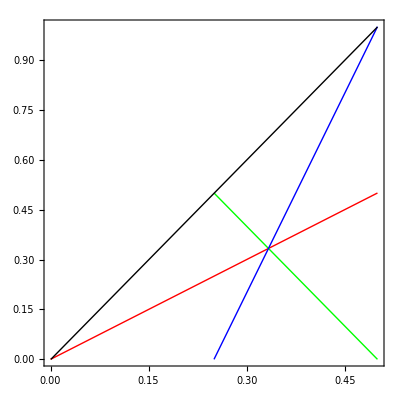

```mathematica
bdryplote=Plot[{E12bdye,E23bdye,E13bdye,2e3-.001},{e3,0,1/2},Frame->True,PlotRange->{0,1},AspectRatio->1,PlotStyle->{Red,Green,Blue,Black},RegionFunction->Function[{e3,x13},x13<2e3]]
```

```mathematica
Solve[E13bdye==E23bdye,e3]
```

{{e3→1/3}}

### Thrust

#### e variables

```mathematica
t12e=t12//.xsubs//.Esubs//FullSimplify
t13e=t13//.xsubs//.Esubs//FullSimplify
t23e=t23//.xsubs//.Esubs//FullSimplify
```

1-2 e3

x_13

2 e3-x_13

#### Plots

```mathematica
τfne[x1_,ee3_]:=If[ee3>1/3,
				If[x1<(E13bdye/.x13->x1/.e3->ee3),
				If[x1<E23bdye/.x13->x1/.e3->ee3,(t13x/.x13->x1/.e3->ee3),(t12e/.x13->x1/.e3->ee3)],
(t23e/.x13->x1/.e3->ee3)],
				If[x1<(E12bdye/.x13->x1/.e3->ee3),(t13x/.x13->x1/.e3->ee3),(t23e/.x13->x1/.e3->ee3)]]
```

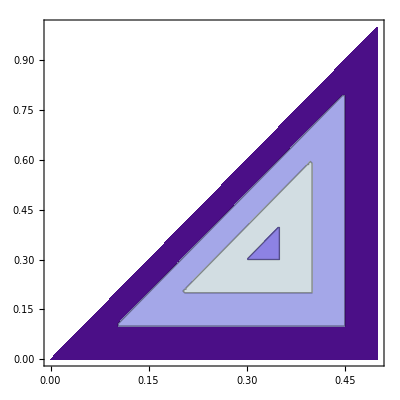

```mathematica
τcontourse=ContourPlot[τfne[x13,e3],{e3,0,1/2},{x13,0,1},RegionFunction->Function[{e3,x13},x13<2e3],Contours->{.1,.2,.3,.4,.5,.6,.7,.8,.9}]
```

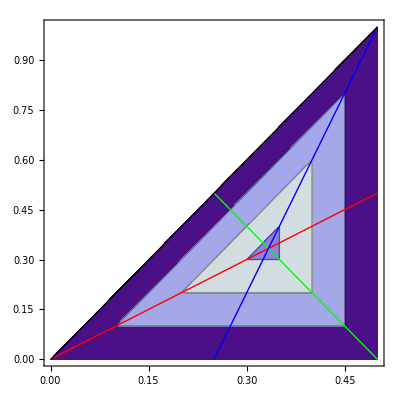

```mathematica
Show[τcontourse,bdryplote]
```

## integrate

### thrust

#### first, the n-collinear

```mathematica
dσnx
```

(2 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^-ϵ ((4 (x_13-1)^2+4 x_23 (x_13-1)+2 (x_23)^2)/(x_13 x_23)-(2 x_23 ϵ)/x_13) μ^(2 ϵ))/(1-ϵ)

```mathematica
ia1=Integrate[dσnx,{x13,0,x23},GenerateConditions->False]/.(x23 b_)^c_->x23^c b^c//FullSimplify
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2) -ϵϵ1-ϵ-x_23/(x_23-1))/ϵ-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ia2=ia1/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

(4 ⅇ^(ℽ ϵ) (x_23)^(-2 ϵ-1) μ^(2 ϵ) (((1-x_23)^-ϵ (x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2))/(ϵ 1-ϵ)-((1-2 x_23)^(1-ϵ) (3 (x_23-1) ϵ-2 x_23+3))/(2-ϵ)))/(2 ϵ-1)

```mathematica
ia3=Integrate[ia2,{x23,0,τ},GenerateConditions->False]
```

-1/((1-2 ϵ)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) (2 τ ϵ^2 (9 ϵ^2-17 ϵ+8) 1-2 ϵϵ2-2 ϵ2 τ+(2 ϵ-1) (2 τ^2 (2-3 ϵ) ϵ^2 2-2 ϵϵ3-2 ϵ2 τ+τ^2 ϵ (2 ϵ^3-4 ϵ^2+3 ϵ-1) 2-2 ϵϵ3-2 ϵτ+(ϵ-1)^2 (-((ϵ-2) -2 ϵϵ1-2 ϵτ+3 ϵ -2 ϵϵ1-2 ϵ2 τ)))-4 τ ϵ (ϵ-1)^2 1-2 ϵϵ2-2 ϵτ)

```mathematica
ia4=Series[ia3,{ϵ,0,0}]//Normal
```

1/3 (-12 τ^2 log(μ)+48 τ log(μ)-48 log(μ) log(τ)+24 log^2(μ)-24 2τ+15 τ^2+6 τ^2 log(1-τ)+12 τ^2 log(τ)+18 τ+24 log^2(τ)-24 τ log(1-τ)-48 τ log(τ)+18 log(1-τ)-π^2)+4/ϵ^2-(2 (-4 log(μ)+τ^2-4 τ+4 log(τ)))/ϵ

```mathematica
ia5=(Series[ia4,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify
```

8 log^2(μ/τ)+4/ϵ^2+(8 log(μ/τ))/ϵ-π^2/3

```mathematica
ib1=Integrate[dσnx,{x13,0,τ},GenerateConditions->False]
```

(4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ (((x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2) -ϵϵ1-ϵ-τ/(x_23-1))/ϵ-((τ+x_23-1) (τ/(x_23-1)+1)^-ϵ ((x_23-3) (ϵ-1)+τ (2 ϵ-1)))/(ϵ-1)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib2=ib1/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

(4 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((x_23 (x_23 (2 (ϵ-1) ϵ+1)-2)-ϵ+2)/ϵ-((τ+x_23-1) (τ/(x_23-1)+1)^-ϵ ((x_23-3) (ϵ-1)+τ (2 ϵ-1)))/(ϵ-1)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib3=Integrate[ib2,{x23,τ,1-2τ},GenerateConditions->False]
```

(4 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^-ϵ (((1-2 τ) τ)^-ϵ ((ϵ-1) τ^ϵ ((ϵ-1) ((ϵ-2)^2 -ϵϵ1-ϵ1-2 τ-(1-2 τ)^2 ϵ (2 ϵ^2-2 ϵ+1) 2-ϵϵ3-ϵ1-2 τ)-2 (2 τ-1) (ϵ-2) ϵ 1-ϵϵ2-ϵ1-2 τ)+ϵ (-τ/(τ-1))^ϵ ((ϵ-1) ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵϵ3-ϵ(2 τ-1)/(τ-1)+(τ-1) (ϵ-2) (-τ+(2 τ-3) ϵ+3) -ϵϵ1-ϵ(2 τ-1)/(τ-1))-(2 τ-1) (ϵ-2) ϵ (-2 τ+(3 τ-4) ϵ+4) 1-ϵϵ2-ϵ(2 τ-1)/(τ-1)))-(-(τ-1) τ)^-ϵ ((ϵ-1) (1-τ)^ϵ ((ϵ-1) ((ϵ-2)^2 -ϵϵ1-ϵτ-τ^2 ϵ (2 ϵ^2-2 ϵ+1) 2-ϵϵ3-ϵτ)+2 τ (ϵ-2) ϵ 1-ϵϵ2-ϵτ)+ϵ ((ϵ-1) (τ^2 (ϵ-1) ϵ 2-ϵϵ3-ϵ-τ/(τ-1)+(τ-1) (ϵ-2) (-τ+(2 τ-3) ϵ+3) -ϵϵ1-ϵ-τ/(τ-1))+τ (ϵ-2) ϵ (-2 τ+(3 τ-4) ϵ+4) 1-ϵϵ2-ϵ-τ/(τ-1)))))/((ϵ-2) (ϵ-1)^2 ϵ^2 (2 ϵ-1) 1-ϵ)

```mathematica
ib4=Series[ib3,{ϵ,0,0}]//Normal
```

4 ((-3 τ^2-8 τ-4 log(1-τ)+4 log(τ)-4 log((1-2 τ) τ)+4 log(-(τ-1) τ)+3) (log(μ)-(log(τ))/2+9/4)+1/2 (-4 21-2 τ+4 2τ+(3 τ^2)/2-4 τ^2 log(τ)+4 τ^2 log(2 τ)-(-6 τ^2+4 τ+4 log(τ)-15) log((1-2 τ) τ)+(-3 τ^2+12 τ+4 log(1-τ)-18) log(-(τ-1) τ)+19 τ-2 log^2(1-τ)+2 log^2(τ)+2 log^2((1-2 τ) τ)-2 log^2(-(τ-1) τ)-4 τ log(τ)+4 τ log(2 τ)+9 log(1-τ)-9 log(τ)-2 (τ-3) (τ-1) log(-τ/(τ-1))-13/2))+(2 (-3 τ^2-8 τ-4 log(1-τ)+4 log(τ)-4 log((1-2 τ) τ)+4 log(-(τ-1) τ)+3))/ϵ

```mathematica
ib5=(Series[ib4,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

16 log(τ) log(μ/τ)+12 log(μ/τ)+4 log^2(τ)+6 log(τ)+(8 log(τ))/ϵ+6/ϵ-(4 π^2)/3+14

```mathematica
ic1indef=Integrate[dσnx,x13]
ic1=((ic1indef/.x13->1/2(1-x23))-(ic1indef/.x13->0))/. 0^(a_)->0
```

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) ((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵx_13/(1-x_23)-2 (x_13)^2 ϵ 2-ϵϵ3-ϵx_13/(1-x_23))-2 x_13 (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵx_13/(1-x_23))

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)2^(ϵ+2) ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (1/2 (x_23-1)-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((1/2 (1-x_23)+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1)+2 x_23-2)-1/2 (1-x_23)^2 ϵ 2-ϵϵ3-ϵ1/2)-(1-x_23) (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2)

```mathematica
ic2indef=Integrate[ic1,x23]
ic2=(ic2indef/.x23->1)-(ic2indef/.x23->1-2τ)
```

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) (x_23)^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-3 x_23 (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵx_23)-(ϵ-1) (2 x_23 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵx_23+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵx_23-2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-ϵ 2-ϵϵ3-ϵ1/2 ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+(ϵ-2) -ϵ2 ϵ1-ϵx_23))))

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-(3 (ϵ-2) ϵ 1-2 ϵ 2-ϵ)/(2-3 ϵ))-(ϵ-1) ((2 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-2 ϵ 2-ϵ)/(2-3 ϵ)+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (((ϵ-1) ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)-(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-ϵ 2-ϵϵ3-ϵ1/2 ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+((ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ)))))-1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (1-2 τ)^-ϵ (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-3 (1-2 τ) (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵ1-2 τ)-(ϵ-1) (2 (1-2 τ) (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵ1-2 τ+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵ1-2 τ-2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-ϵ 2-ϵϵ3-ϵ1/2 ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+(ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ))))

```mathematica
ic3=Series[ic2,{ϵ,0,0}]//Normal
```

1/3 (48 τ^2 log(μ)+48 τ log(μ)+48 log(μ) log(1-2 τ)+48 21-2 τ+30 τ^2-24 τ^2 log(1-2 τ)-48 τ^2 log(2 τ)+24 τ^2 log(2)+150 τ-12 log^2(1-2 τ)-24 τ log(1-2 τ)-48 τ log(2 τ)+24 τ log(2)+24 log(2) log(1-2 τ)+39 log(1-2 τ)-8 π^2)+(8 (τ^2+τ+log(1-2 τ)))/ϵ

```mathematica
ic4=(Series[ic3,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

0

```mathematica
τn=Series[ia5+ib5+ic4/.Log[μ/τ]->1/2 Log[μ^2]-Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
2 Log[μsq/τ]- Log[μsq/τ^2]//PowerExpand//Expand
2Log[μsq/τ]^2-Log[μsq/τ^2]^2//PowerExpand//Expand
Log[μsq/τ]//PowerExpand//Expand
```

log(μsq)

log^2(μsq)-2 log^2(τ)

log(μsq)-log(τ)

```mathematica
τnSCfactor=Series[Expand[Normal[τn]]/. Log[μ^2]/ϵ->2 Log[μ^2/τ]/ϵ- Log[μ^2/τ^2]/ϵ/.  Log[μ^2]^2->2Log[μ^2/τ]^2-Log[μ^2/τ^2]^2+2Log[τ]^2/.Log[μ^2]->Log[μ^2/τ]+ Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(-4 log(μ^2/τ^2)+8 log(μ^2/τ)+6)/ϵ+(-2 log^2(μ^2/τ^2)+4 log^2(μ^2/τ)+6 log(μ^2/τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
%//PowerExpand//ExpandAll
Normal[τn]//PowerExpand//ExpandAll
```

4/ϵ^2+(8 log(μ)+6)/ϵ+(8 log^2(μ)+12 log(μ)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

8 log^2(μ)+12 log(μ)-4 log^2(τ)-6 log(τ)+4/ϵ^2+(8 log(μ))/ϵ+6/ϵ-(5 π^2)/3+14

```mathematica
τrate=(τn-2Z2+2C2//PowerExpand)//ExpandAll//Normal
```

-4 log^2(τ)-6 log(τ)+(2 π^2)/3-2

#### next, show that the nbar collinear piece cancels with the overlap

```mathematica
dσnbx=dσnx/.x13->x23b/.x23->x13/.x23b->x23//ExpandAll//Simplify
```

-(4 ⅇ^(ℽ ϵ) (x_13)^(-ϵ-1) (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13)^2 (ϵ-1)-2 (x_23-1) x_13-2 (x_23-1)^2) μ^(2 ϵ))/(1-ϵ)

```mathematica
ia1b=Integrate[dσnbx,{x13,0,x23},GenerateConditions->False]/.(x23 b_)^c_->x23^c b^c//FullSimplify
```

-1/((2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-2 ϵ-1) μ^(2 ϵ) ((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ -ϵϵ1-ϵ-x_23/(x_23-1)+(1-x_23)^ϵ (x_23 (ϵ-4)+ϵ+3) (1-2 x_23)^(1-ϵ))

```mathematica
ia2b=ia1b/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

-(2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-2 ϵ-1) μ^(2 ϵ) ((1-x_23)^ϵ (x_23 (ϵ-4)+ϵ+3) (1-2 x_23)^(1-ϵ)+((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ)/(1-ϵ)))/((2 ϵ-1) 1-ϵ)

```mathematica
ia3b=Integrate[ia2b,{x23,0,τ},GenerateConditions->False]
```

-1/(ϵ^2 (2 ϵ-1) 1-ϵ)ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) (1/(1-2 ϵ)2 τ ϵ (2 (ϵ^2-5 ϵ+4) 1-2 ϵϵ2-2 ϵτ-1/(2-2 ϵ)(τ (1-2 ϵ) (ϵ-4) ((ϵ-1) 2-2 ϵϵ3-2 ϵτ+2 ϵ 2-2 ϵϵ3-2 ϵ2 τ)-2 (ϵ-1) ϵ (ϵ+10) 1-2 ϵϵ2-2 ϵ2 τ))+(ϵ^2-5 ϵ+4) -2 ϵϵ1-2 ϵτ-ϵ (ϵ+3) -2 ϵϵ1-2 ϵ2 τ)

```mathematica
ia4b=Series[ia3b,{ϵ,0,0}]//Normal
```

1/3 (-24 τ^2 log(μ)+96 τ log(μ)-48 log(μ) log(τ)+24 log^2(μ)-24 2τ-3 τ^2+12 τ^2 log(1-τ)+24 τ^2 log(τ)+108 τ+24 log^2(τ)-48 τ log(1-τ)-96 τ log(τ)+36 log(1-τ)-π^2)+4/ϵ^2-(4 (-2 log(μ)+τ^2-4 τ+2 log(τ)))/ϵ

```mathematica
ia5b=(Series[ia4b,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify
```

8 log^2(μ/τ)+4/ϵ^2+(8 log(μ/τ))/ϵ-π^2/3

```mathematica
ib1b=Integrate[dσnbx,{x13,0,τ},GenerateConditions->False]
```

-1/((2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ -ϵϵ1-ϵ-τ/(x_23-1)+(τ+x_23-1) (τ+x_23 (ϵ+3)-(2 τ+1) ϵ-3) (τ/(x_23-1)+1)^-ϵ)

```mathematica
ib2b=ib1b/.Hypergeometric2F1Regularized[a_,b_,c_,z_]:>Hypergeometric2F1[a,b,c,z]/Gamma[c]/.Hypergeometric2F1[a_,b_,c_,z_]:>Series[Hypergeometric2F1[a,b,c,z],{ϵ,0,0}]//Normal
```

-(2 ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (x_23)^(-ϵ-1) μ^(2 ϵ) τ^-ϵ ((τ+x_23-1) (τ+x_23 (ϵ+3)-(2 τ+1) ϵ-3) (τ/(x_23-1)+1)^-ϵ+((x_23-1)^2 (ϵ-4) (ϵ-1) -ϵ)/(1-ϵ)))/((2 ϵ-1) 1-ϵ)

```mathematica
ib3b=Integrate[ib2b,{x23,τ,1-2τ},GenerateConditions->False]/.(-τ/a_)^b_.->τ^b (-a)^(-b)/.(τ a_)^b_.->τ^b a^b//Simplify
```

-1/((ϵ-1) ϵ (2 ϵ-1) 1-ϵ)2 ⅇ^(ℽ ϵ) μ^(2 ϵ) τ^(-2 ϵ) ((1-2 τ)^-ϵ τ^ϵ (1/(ϵ-2)(1-τ)^-ϵ ((ϵ-1) ((τ-1) (ϵ-2) (-τ+2 τ ϵ+ϵ+3) -ϵϵ1-ϵ(2 τ-1)/(τ-1)-(1-2 τ)^2 ϵ (ϵ+3) 2-ϵϵ3-ϵ(2 τ-1)/(τ-1))-(2 τ-1) (ϵ-2) ϵ (-4 τ+(τ+2) ϵ+6) 1-ϵϵ2-ϵ(2 τ-1)/(τ-1))+((ϵ-4) (ϵ-1)^2 ϵ-2-ϵ1-ϵ1-2 τ)/ϵ)-(1-τ)^-ϵ (1/(ϵ-2)((ϵ-1) ((τ-1) (ϵ-2) (-τ+2 τ ϵ+ϵ+3) -ϵϵ1-ϵτ/(1-τ)-τ^2 ϵ (ϵ+3) 2-ϵϵ3-ϵτ/(1-τ))+τ (ϵ-2) ϵ (-4 τ+(τ+2) ϵ+6) 1-ϵϵ2-ϵτ/(1-τ))+((ϵ-4) (ϵ-1)^2 (1-τ)^ϵ ϵ-2-ϵ1-ϵτ)/ϵ))

```mathematica
ib4b=Series[ib3b,{ϵ,0,0}]//Normal
```

-24 τ^2 log(μ)-64 τ log(μ)-16 log(μ) log(1-2 τ)+16 log(μ) log(τ)+24 log(μ)-8 21-2 τ+8 2τ-36 τ^2+18 τ^2 log(1-2 τ)-4 τ^2 log(1-τ)+6 τ^2 log(τ)+16 τ^2 log(2 τ)-60 τ+4 log^2(1-2 τ)-12 log^2(τ)+8 τ log(1-2 τ)+16 τ log(1-τ)+56 τ log(τ)+16 τ log(2 τ)-12 log(1-2 τ)-12 log(1-τ)+8 log(1-2 τ) log(τ)-12 log(τ)+(-12 τ^2-32 τ-8 log(1-2 τ)+8 log(τ)+12)/ϵ+24

```mathematica
ib5b=(Series[ib4b,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

16 log(τ) log(μ/τ)+24 log(μ/τ)+4 log^2(τ)+12 log(τ)+(8 log(τ))/ϵ+12/ϵ-(4 π^2)/3+24

```mathematica
ic1indef=Integrate[dσnx,x13]
ic1=((ic1indef/.x13->1/2(1-x23))-(ic1indef/.x13->0))/. 0^(a_)->0
```

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)4 ⅇ^(ℽ ϵ) (x_13)^-ϵ (-x_13-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((x_13+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) ((x_23)^2 (ϵ-1)+2 x_23-2) -ϵϵ1-ϵx_13/(1-x_23)-2 (x_13)^2 ϵ 2-ϵϵ3-ϵx_13/(1-x_23))-2 x_13 (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵx_13/(1-x_23))

1/((ϵ-2) (ϵ-1) ϵ 1-ϵ)2^(ϵ+2) ⅇ^(ℽ ϵ) (1-x_23)^-ϵ (1/2 (x_23-1)-x_23+1)^-ϵ (x_23)^(-ϵ-1) ((1/2 (1-x_23)+x_23-1)/(x_23-1))^ϵ μ^(2 ϵ) ((ϵ-1) ((ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1)+2 x_23-2)-1/2 (1-x_23)^2 ϵ 2-ϵϵ3-ϵ1/2)-(1-x_23) (x_23-2) (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2)

```mathematica
ic2indef=Integrate[ic1,x23]
ic2=(ic2indef/.x23->1)-(ic2indef/.x23->1-2τ)
```

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) (x_23)^-ϵ μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-3 x_23 (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵx_23)-(ϵ-1) (2 x_23 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵx_23+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((x_23)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵx_23-2 (ϵ-2) -ϵ2 ϵ1-ϵx_23)-ϵ 2-ϵϵ3-ϵ1/2 ((x_23)^2 ϵ 2-ϵ2 ϵ3-ϵx_23+(ϵ-2) -ϵ2 ϵ1-ϵx_23))))

1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-(3 (ϵ-2) ϵ 1-2 ϵ 2-ϵ)/(2-3 ϵ))-(ϵ-1) ((2 (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-2 ϵ 2-ϵ)/(2-3 ϵ)+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 (((ϵ-1) ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)-(2 (ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ))-ϵ 2-ϵϵ3-ϵ1/2 ((ϵ 1-2 ϵ 3-ϵ)/(3-3 ϵ)+((ϵ-2) 1-2 ϵ -ϵ)/(3 -3 ϵ)))))-1/((ϵ-2)^2 (ϵ-1)^2 ϵ^2 1-ϵ)2^(ϵ+1) ⅇ^(ℽ ϵ) μ^(2 ϵ) (1-2 τ)^-ϵ (-2 (ϵ-2) ϵ 1-ϵϵ2-ϵ1/2 ((ϵ-1) ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-3 (1-2 τ) (ϵ-2) ϵ 1-ϵ2 ϵ2-ϵ1-2 τ)-(ϵ-1) (2 (1-2 τ) (ϵ-2) ϵ (ϵ 2-ϵϵ3-ϵ1/2+2 (ϵ-2) -ϵϵ1-ϵ1/2) 1-ϵ2 ϵ2-ϵ1-2 τ+(ϵ-1) (2 (ϵ-2) -ϵϵ1-ϵ1/2 ((1-2 τ)^2 (ϵ-1) ϵ 2-ϵ2 ϵ3-ϵ1-2 τ-2 (ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ)-ϵ 2-ϵϵ3-ϵ1/2 ((1-2 τ)^2 ϵ 2-ϵ2 ϵ3-ϵ1-2 τ+(ϵ-2) -ϵ2 ϵ1-ϵ1-2 τ))))

```mathematica
ic3=Series[ic2,{ϵ,0,0}]//Normal
```

1/3 (48 τ^2 log(μ)+48 τ log(μ)+48 log(μ) log(1-2 τ)+48 21-2 τ+30 τ^2-24 τ^2 log(1-2 τ)-48 τ^2 log(2 τ)+24 τ^2 log(2)+150 τ-12 log^2(1-2 τ)-24 τ log(1-2 τ)-48 τ log(2 τ)+24 τ log(2)+24 log(2) log(1-2 τ)+39 log(1-2 τ)-8 π^2)+(8 (τ^2+τ+log(1-2 τ)))/ϵ

```mathematica
ic4=(Series[ic3,{τ,0,0}]//Normal)/.Log[μ]->Log[μ/τ]+Log[τ]//Simplify//Expand
```

0

```mathematica
τn=Series[ia5+ib5+ic4/.Log[μ/τ]->1/2 Log[μ^2]-Log[τ]//ExpandAll,{ϵ,0,0}]
```

4/ϵ^2+(4 log(μ^2)+6)/ϵ+(2 log^2(μ^2)+6 log(μ^2)-4 log^2(τ)-6 log(τ)-(5 π^2)/3+14)+O(ϵ^1)

```mathematica
τrate=(τn-2Z2+2C2//PowerExpand)//ExpandAll//Normal
```

-4 log^2(τ)-6 log(τ)+(2 π^2)/3-2